# Free undamped linear oscillations of a sagging cable and a discrete chain

It’s a story of differentiation and first-order approximations - again, and again, and again...

Rauan Kaldybayev

This work uses Newton’s second law to analyze small oscillations of a catenary cable and a hanging discrete chain. Rigidity, air resistance, friction, and stretching or compression due to axial stress are neglected. The cable is of uniform density, and the chain is made of many identical point masses connected by rigid massless rods of equal length. The work aimed to compare the oscillations of a catenary cable to those of a tight string. It was expected to find dispersion and nonlocality in a sagging cable, and these effects were indeed observed. One unexpected finding was that the partial differential equation governing in-plane oscillations is of fourth-order and includes mixed space and position derivatives. The work also studies the oscillations of a hanging discrete chain; it was found that a chain with a large number of elements oscillates like a continuous cable.
	To check the correctness of the work, the predicted natural frequencies were compared to those given by John Gregg Gale in his 1976 master’s thesis. The results matched, suggesting that the current computational essay is most likely correct.
	The work is useful primarily from the theoretical standpoint to better understand the physics of oscillations, as the systems explored here exhibit exotic behaviors like nonlocality. Empirical observations made here lead to a general conjecture regarding oscillatory systems: the existence of “natural coordinates” (explained later in the abstract). The essay can also be used to estimate the frequencies of conductor galloping, which is a major question in engineering.
	The first novelty of this essay is that it uses a unique approach that is based on curvilinear coordinates, as opposed to past works, which used a more visual approach. The present work is more formal: it starts with Newton’s second law and the incompressibility condition and transforms the equations in various ways using geometrical identities. The equations of motion yielded by this method are written in terms of the cable’s perpendicular displacement only, as opposed to other works, which also used quantities like angles. This can make the physical meaning of the equations more transparent.
	The two PDEs have variable coefficients and include second-order time derivatives. The first equation describes horizontal oscillations and includes second-order position derivatives. The second equation describes in-plane oscillations and involves fourth-order position derivatives and mixed derivatives. The PDEs are independent.
Arc length, displacement of the cable from equilibrium, and Cartesian coordinates are the most intuitive coordinates for the problem. Turns out, they also have convenient mathematical properties. The normal modes of horizontal oscillations are orthogonal when arc length is used as the spatial coordinate. The equations of motion of the cable are independent when written in terms of the cable’s horizontal and in-plane displacement from equilibrium. The PDEs describing the cable’s oscillations have polynomial coefficients when the vertical coordinate z is used as the spatial coordinate. The PDE describing the normal mods of horizontal oscillations takes the simple form ψ''[χ] + ϖ^2 Cosh[χ] ψ[χ] = 0 when the horizontal coordinate x is used as the spatial coordinate. Maybe in general, every system has its own “natural coordinates”, which are most convenient when studying the system and can be guessed from physical intuition?
	Having derived the equations of motion, the work explores their behavior in the limiting cases, when the cable is hung very tightly (e.g. its ends are pulled far from each other and the cable straightens out) and when the cable has a large sag (e.g. when its endpoints are brought together, almost touching each other). While the equations are generally complicated and couldn’t be solved analytically, their behavior in these limiting cases is comparatively simple. For a lax cable, the normal modes can be expressed through Bessel functions. For a tight cable, an approximate algebraic formula for the natural frequencies and normal modes is given. The formula is quick to compute numerically but can be difficult to analyze due to the presence of hypergeometric functions. Saxon and Cahn’s 1953 article gives a different estimate for the natural frequencies.
	Empirically, it was observed that the normal modes have greater curvature and amplitude near the cable’s lowest point, and near the edges, they flatten out and decrease in amplitude. This is because tension is lowest at the bottom of the cable and increases from there.
	The equations of horizontal and in-plane oscillations of a sagging discrete chain are, respectively, d^2/dt^2 θ = -Y θ, d^2/dt^2 φ = - K φ, where θ and φ are vectors of dimension N and N - 1, respectively, for N ∈ Z^+, and Y and K are square matrices of corresponding dimensions. It was empirically observed that a chain with a large number of elements oscillates like a continuous cable – it has the same natural frequencies and normal modes, and the eigenvalues of the matrices Y and K converge to certain limits.
	In addition, the essay features many visualizations and illustrations (including interactive animations), which make the content more intuitive. It also includes Wolfram Language code, which can often give a clearer picture, for example, when illustrating a numerical method.
	To study the oscillations of a catenary cable, the essay starts by finding the cable’s equilibrium configuration; in addition to mathematical formulas, it presents Wolfram Language functions to automatically compute the cable’s shape. Curvilinear coordinates fitted to the cable’s equilibrium shape are defined. Two PDEs describing the cable’s small oscillations are derived from Newton’s second law, incompressibility condition, and geometrical identities. The PDEs are non-dimensionalized and solved as a superposition of their normal modes. The normal modes could not be found analytically, so an approach based on Frobenius’s method was used. The solution was calculated automatically using frobeniusDSolve, a Wolfram Language function was written as a part of the project. The function has many possible applications in other problems.
	To study the oscillations of a discrete chain, Newton’s second law is first written, and the equilibrium is found; Wolfram Language functions are presented alongside mathematical formulas. Newton’s 2nd law is linearized to explore small oscillations. Using boundary conditions, two independent ODEs of motion are then obtained: d^2/dt^2 θ = -Y θ, d^2/dt^2 φ = - K φ, where θ and φ are vectors and Y and K are square matrices. Natural frequencies and normal modes are computed through the eigenvalues and eigenvectors of these matrices. Empirically it is observed that the normal modes and natural frequencies of a discrete chain with a large number of elements are the same as those of a continuous cable.

## Introduction

## Why is this interesting?

The original motivation for this work came from the YouTube video where a stay cable was hit with a wrench and produced awesome Star Wars blaster sounds. I looked up some articles on this topic and was immediately fascinated - not by the sound, however, but by the oscillations themselves.
	A vibrating string - a classic example of an oscillatory system. The system is governed by the wave equations (∂^2 y)/(∂t^2) = (∂^2 y)/(∂x^2), the normal modes of which are sine functions, and the dispersion relation is linear - simple. If we have two strings with different densities are connected to each other, things get more interesting. A pulse travelling from one string to another would partially reflect at the sewing point because of impedance mismatch. Things are even more interesting when a string is hung vertically and impedance changes continuously. The normal modes are then written through Bessel functions, and dispersion appears. We can see that from a simple string, we can get a wide range of fascinating behaviors.
	But what if we go a bit further and hang the string from two points that are not on the same vertical, such that the string would be sagging? How would the string oscillate then? There are many effects we would expect: dispersion due to variable tension, pulses “continuously reflecting” when travelling because of changing tension. We might even expect nonlocality - if we pick such a string at one point, the entire string will have to move immediately because otherwise its length would change. As for the normal modes of this system, even trying to imagine them is difficult.
	The problem discussed in here is interesting first of all from the theoretical standpoint. It can be curious to people interested in the physics of oscillations and to students learning about the topic. As mentioned above, the system features interesting phenomena like dispersion, “continuous reflection”, and nonlocality; in addition, as will be shown below, one of the PDEs describing the cable’s oscillations actually contains fourth-order position derivatives and mixed position and time derivatives, which is quite exotic for Newtonian mechanics. The results reached in this work can also be applied on practice to estimate the normal frequencies of conductor galloping, which is a very relevant issue in engineering. There exist more accurate models of conductor galloping, however, the model presented here is particularly simple because it’s linear; the theory can be helpful as a first introduction.

## Cable in equilibrium; Cartesian coordinates

A cable is hung between two fixed points - let’s call them O and P. The force of gravity pulls the cable down, but the force of tension keeps it from falling. In equilibrium, the cable takes a shape that minimizes its potential energy. The shape is known as catenary:

-Graphics3D-

To describe the system, we can use Cartesian coordinates where the point O is the origin of coordinates, the z axis goes vertically upward (against the force of gravity), and the x axis goes horizontally such that the points O and P lie in the x-z plane. In these coordinates, the equilibrium shape of the cable is given by the function z_e[x]:

z_e[x] = Λ (Cosh[(x - x_0)/Λ] - Cosh[x_0/Λ])

Here Λ and x_0 are constants determined from the boundary conditions, e.g. are picked such that the curve would pass through the points O and P. The subscript e in z_e[x] denotes that the function describes the cable’s equilibrium. In equilibrium, the cable lies in the x-z plane, so

y_e[x] = 0

The meaning of the functions y_e[x] and z_e[x] is that if we pick some point on the cable when it’s in equilibrium, then the coordinates x, y, z of this point would be related by (1) and (2). When the cable is displaced from equilibrium, its shape would of course be different, and the functions y[x] and z[x] would be different from y_e[x] and z_e[x].

#### Code used to generate the figure

```mathematica
With[{xp = 3, Λ = 1, x0 = 1}, Labeled[
	Show[{
		ParametricPlot3D[
			{x, 0, Λ(Cosh[(x - x0)/Λ] - Cosh[x0/Λ])},
			{x, 0, xp},
			PlotStyle -> {Darker@Green, Thick}, PlotRange->{Automatic, {-1.4, 1.4},  Automatic}
		],
		Graphics3D[{
			{Arrow[{{0, 0, 0}, {0.7, 0, 0}}]}, {Text[Style["X", Bold, 12, FontFamily -> "Computer Modern"], {0.9, 0, 0}]},
			{Arrow[{{0, 0, 0}, {0, 0.7, 0}}]}, {Text[Style["Y", Bold, 12, FontFamily -> "Computer Modern"], {0, 0.9, 0}]},
			{Arrow[{{0, 0, 0}, {0, 0, 0.7}}]}, {Text[Style["Z", Bold, 12, FontFamily -> "Computer Modern"], {0, 0, 0.9}]},
			{Opacity[0.1], InfinitePlane[{{0, 0, 0}, {1, 0, 0}, {0, 0, 1}}]},
			{PointSize[Large], Point[{0, 0, 0}]}, {Text[Style["O", Bold, 12, FontFamily -> "Computer Modern"], {0, -0.4, 0}]},
			{PointSize[Large], Point[{xp, 0, Λ(Cosh[(xp - x0)/Λ] - Cosh[x0/Λ])}]}, {Text[Style["P", Bold, 12, FontFamily -> "Computer Modern"], {xp, -0.4, Λ(Cosh[(xp - x0)/Λ] - Cosh[x0/Λ])}]}
		}]
	}, ImageSize -> Medium, ViewPoint -> {2.1, -2.7, 0.9}],
	LineLegend[{Darker@Green}, {"Cable in equilibrium"}]
]]
```

## Assumptions regarding the cable’s physical properties

This work neglects friction and air resistance, the cable’s stiffness, and stretching and compression due to axial stresses.

From physical intuition, we can guess that air resistance is negligible for massive cables. A small grain of dust is easily dragged by the air and can float for a while, while a large boulder can only be moved by storms. The stiffness of the cable can also be neglected for large cables. When Titanic capsized and its bow rose into the air, the ship broke in half under its own weight; the force of gravity dominated the structure’s strength. On the other hand, a smaller model of the same ship can easily support itself; elastic forces are much stronger than the force of gravity. This shows that the larger the object, the more gravity dominates elastic forces.

-Graphics--Graphics-

On the left, you see an illustration of Titanic breaking in half due to the mechanical stresses (taken from https://www.britannica.com/story/timeline-of-the-titanics-final-hours). On the right is shown a smaller model of Titanic; the model can easily support its weight even though it sits on a narrow base.

The third assumption is that we can neglect compression and stretching due to axial stresses. To see that this approximation is valid, let us use Hooke’s law, which states that the relative elongation of a small piece of cable is given by ε = σ/E, where σ is stress and E is the Young modulus of the cable’s material, say steel. To estimate the order of magnitude of σ, we can use dimensional analysis, which yields that σ ~ ρ g L, where ρ is the density of steel, g is the free fall acceleration, and L is the cable’s length. For ε, we then have ε ~ (ρ g L)/E. For ε to be less than 10^-3, L must be smaller than approximately 2500 meters (taking ρ = 8000, g = 10, E = 2 · 10^11, all in SI units). We conclude that the third approximation that stretching and compression due to axial stresses are negligible for cables under 2500 meters in length, or basically for all cables we would normally see. Thus, we third assumption is also sensible.

### Small oscillations

The current work investigates small oscillations, when the cable is only displaced a little bit from the equilibrium. This assumption can be formulated mathematically the following way. The configuration of the cable can be described using generalized coordinates; if q is one of those coordinates, then we have

q = q_e + O[ε]

where q_e is the value of q in equilibrium and ε is a small number. Although this is not true for a general system, the current work assumes that for each generalized coordinate, there is exactly one equilibrium value; there is only one equilibrium configuration for a cable hung between two points, so it only makes sense if the generalized coordinates describing it also have only one equilibrium value.
	For small oscillations, ε << 1. This means that in an expression of the form a_0 + a_1 ε + a_2 ε^2 + ... + a_n ε^n, we may only leave the first few terms, as all the following terms would be negligibly small. Most of the times, we would only leave the a_0 term.

## Curvilinear coordinates

## Definition

When studying small oscillations of a given system, it is convenient to choose coordinates that are somehow fitted to the system’s equilibrium. When studying a mathematical pendulum, the angle between the rope and the vertical is most often used as the coordinate. In the case of a hanging cable, it is  convenient to use curvilinear coordinates fitted to the cable’s equilibrium.

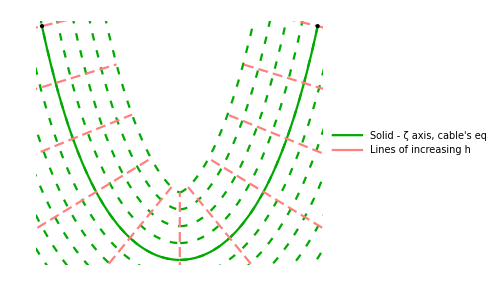

Let’s first look at the x-z plane. We know that in equilibrium, the cable takes the shape of a catenary. So, an intuitive way to measure the cable’s displacement from equilibrium would be to take the signed distance from the equilibrium catenary as one of the coordinates - let’s call it h. The coordinate h of a given point in the x-z plane is the signed distance from that point to the catenary described by (1); if the point is above the equilibrium catenary, then h is positive, and if the point is below the equilibrium catenary, then h is negative. Now, to coordinatize the two-dimensional x-z plane, we need two coordinates and not just one. Let us name the second coordinate ζ and define it the following way. To determine the coordinate ζ of a given point A, take the point C on the equilibrium catenary that is closest to A. The coordinate ζ_A of the point A is defined to be the arc length along the equilibrium catenary from the point O to the point C. As you can see from the figure below, ζ_A = OC, h_A = ±AC.

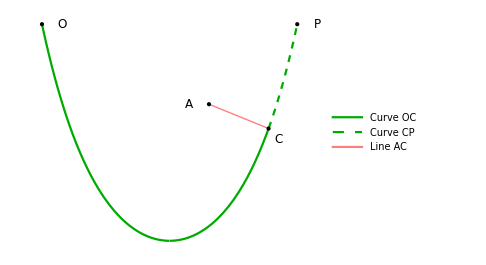

Now, to coordinatize three-dimensional space, we need one more coordinate. Since in equilibrium the cable rests in the x-z plane, the Cartesian coordinate y would work just fine. To extend the coordinates ζ and h into three-dimensional space, we can do the following thing. For a given point A, take the perpendicular from A to the x-z plane. Call the intersection of this perpendicular with the x-z plane D. We then have, y_A = ±AD, h_A = ±CD, ζ_A = OC. On the figure below, y_A is negative.

-Graphics3D-

The coordinates ζ_A, y_A, h_A  of the point A tells us exactly where the point A is. Mathematically, we can write

r^– = r^–[ζ, y, h]

Where r^– is the position vector of a point. The formula above simply says that the position of a point can be described using the coordinates ζ, y, h. The explicit transformation formula from ζ, h to x, z can be found from the formula (1) and the definition of ζ and h.

x[ζ, h] = x_0 + Λ ArcSinh[(ζ - l_0)/Λ] - ((ζ - l_0)/Λ)/(√(1  + ((ζ - l_0) / Λ)^2)) h
z[ζ, h] = Λ (√(1 + ((ζ - l_0)/Λ)^2) - √(1 + (l_0/Λ)^2)) + 1/(√(1  + ((ζ - l_0) / Λ)^2)) h

#### Code used to generate the figures

```mathematica
ClearAll[findLambda];
findLambda[L_, xp_, zp_] := With[
	{
		D = Sqrt[L^2 - zp^2] / xp
	},
	If[(!Element[D, Reals]) || (D < 1),
		$Failed,
		(If[#[[1, 2]] > 0, xp / (2 #[[1, 2]]), Nothing]& /@ 
			NSolve[D == Sinh[ϕ] / ϕ, ϕ, Reals, WorkingPrecision -> MachinePrecision])[[1]]
	]
];
```

```mathematica
ClearAll[findX0];
findX0[L_, xp_, zp_, Λ_] := xp / 2 - Λ ArcTanh[zp / L];
```

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, ζbar, hbar,
		ζlines, hlines, ζ, h
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	ζbar = Function[ζ, {1, (ζ - l0)/Λ}/(√(1 + (ζ - l0)^2/Λ^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	ζlines = Plus[# hbar[ζ], {xe[ζ], ze[ζ]}]& /@ Range[-2Λ, Λ, Λ/4];
	hlines = Plus[h hbar[#], {xe[#], ze[#]}]& /@ Range[0, L, L/10];
	
	Legended[Show[{
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, 0, L},
			PlotStyle -> {Thick, Darker@Green},
		Axes -> False
		],
		ParametricPlot[ζlines,
			{ζ, -L, 2L},
			PlotStyle -> Array[{Thin, Dashing[{0.015, 0.02}], Darker@Green}&, Length@ζlines]
		],
		ParametricPlot[hlines,
			{h, -2Λ, Λ},
			PlotStyle -> Array[{Thin, Dashing[{0.02, 0.01}], Pink}&, Length@ζlines]
		],
		Graphics[{
			{PointSize[Large], Point[{0, 0}]},
			{PointSize[Large], Point[{xp, zp}]}
		}]
	}, ImageSize -> Medium], LineLegend[{Darker@Green, Pink},
	{"Solid - ζ axis, cable's equilibrium shape\nDashed - lines of increasing ζ", "Lines of increasing h"}]]
]
```

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, hbar,
		ζ, h,
		ζA = 1.6, hA = 0.25
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	Legended[Show[{
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, 0, ζA},
			PlotStyle -> {Thick, Darker@Green},
			Axes -> False
		],
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, ζA, L},
			PlotStyle -> {Thick, Dashed, Darker@Green},
			Axes -> False
		],
		Graphics[{
			{PointSize[Large], Point[{0, 0}]},
			{PointSize[Large], Point[{xp, zp}]},
			{Thick, Pink, Line[{{xe[ζA], ze[ζA]}, {xe[ζA], ze[ζA]} + hA hbar[ζA]}]},
			{PointSize[Large], Point[{xe[ζA], ze[ζA]} + hA hbar[ζA]]}, {Text[Style["A", 12], {xe[ζA], ze[ζA]} + hA hbar[ζA] - {0.08, 0}]},
			{PointSize[Large], Point[{xe[ζA], ze[ζA]}]}, {Text[Style["C", 12], {xe[ζA], ze[ζA]} + {0.04, -0.04}]},
			{Text[Style["O", 12], {0.08, 0}]},
			{Text[Style["P", 12], {xe[L], ze[L]} + {0.08, 0}]}
		}]
	}, ImageSize -> Medium, PlotRange -> All], LineLegend[{Darker@Green, {Thick, Dashed, Darker@Green}, Pink},
	{"Curve OC", "Curve CP", "Line AC"}]]
]
```

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, hbar,
		ζ, h,
		ζA = 1.6, yA = -0.4, hA = 0.25
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 0, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	Legended[Show[{
		ParametricPlot3D[{xe[ζ], 0, ze[ζ]},
			{ζ, 0, ζA},
			PlotStyle -> {Thick, Darker@Green},
			Axes -> False
		],
		ParametricPlot3D[{xe[ζ], 0, ze[ζ]},
			{ζ, ζA, L},
			PlotStyle -> {Thick, Dashed, Darker@Green},
			Axes -> False
		],
		Graphics3D[{
			{Opacity[0.1], InfinitePlane[{{0, 0, 0}, {0, 0, 1}, {1, 0, 0}}]},
			{PointSize[Large], Point[{0, 0, 0}]},
			{PointSize[Large], Point[{xp, 0, zp}]},
			{Thick, Pink, Line[{{xe[ζA], 0, ze[ζA]}, {xe[ζA], 0, ze[ζA]} + hA hbar[ζA]}]},
			{Thick, Darker@Cyan, Line[{{xe[ζA], 0, ze[ζA]} + hA hbar[ζA], {xe[ζA], yA, ze[ζA]} + hA hbar[ζA]}]},
			{PointSize[Large], Point[{xe[ζA], yA, ze[ζA]} + hA hbar[ζA]]}, {Text[Style["A", 12], {xe[ζA], yA, ze[ζA]} + hA hbar[ζA] - {0.08, 0, 0}]},
			{PointSize[Large], Point[{xe[ζA], 0, ze[ζA]} + hA hbar[ζA]]}, {Text[Style["D", 12], {xe[ζA], 0, ze[ζA]} + hA hbar[ζA] - {0.08, 0, 0}]},
			{PointSize[Large], Point[{xe[ζA], 0, ze[ζA]}]}, {Text[Style["C", 12], {xe[ζA], 0, ze[ζA]} + {0.04, 0, -0.04}]},
			{Text[Style["O", 12], {0.08, 0, 0}]},
			{Text[Style["P", 12], {xe[L], 0, ze[L]} + {0.08, 0, 0}]}
		}]
	}, ImageSize -> Medium, PlotRange -> All, ViewPoint -> {0.7, -0.4, 0.6}], LineLegend[{Darker@Green, {Thick, Dashed, Darker@Green}, Pink, Darker@Cyan},
	{"Curve OC", "Curve CP", "Line DC", "Line AD"}]]
]
```

## About basis vectors

Let us define the basis vectors ζ^̑, y^̑, h^̑ as

ζ^̑ ≡ (∂r^–)/(∂ζ)
y^̑ ≡ (∂r^–)/(∂y)
h^̑ ≡ (∂r^–)/(∂h)

where r^–[ζ, y, h] is given by (4). The physical meaning of ζ^̑ is that if we increase the coordinate ζ of a point by some infinitesimal value dζ, then it would move by ζ^̑ dζ, and the same is true of y^̑ and h^̑. Now, from the figure before the equation (4) we can see that the basis vectors ζ^̑, y^̑, h^̑ are orthogonal. This can be proven by “brute force” algebra from (5), but here is a visual explanation. Increasing y_A while leaving h_A and ζ_A the same means increasing AD while leaving CD and OC the same, or basically moving the point A away or toward the x-z plane; thus, y^̑ is directed along AD. Similarly, we get that h^̑ is directed along the line CD. Since AD is perpendicular to the x-z plane, we conclude that y^̑ and h^̑ are orthogonal. Increasing the coordinate ζ_A leaving y_A and h_A constant means moving the point C further along the equilibrium catenary while holding AD and CD the same. From here, we see that the basis vector ζ^̑ is directed along the tangent line to the equilibrium catenary at the point C. Since CD is perpendicular to the equilibrium catenary, ζ^̑ is orthogonal to h^̑; and since AD is perpendicular to the x-z plane and ζ^̑ lies in the x-z plane, we get that ζ^̑ is also orthogonal to y^̑.

ζ^̑ · y^̑ = 0
ζ^̑ · h^̑ = 0
y^̑ · h^̑ = 0

Now, y_A is defined to be the distance from A to the x-z plane, and h_A is the distance from A to the equilibrium catenary. The coordinates y and h are distances, so (y^̑)^2 = (h^̑)^2 = 1.

y^̑ · y^̑ = 1
h^̑ · h^̑ = 1

The norm of ζ^̑ is generally a function of position, however, it equals 1 when y = h = 0, and here is why. If the coordinates y_A and h_A of the point A are both zero, then the point A lies on the equilibrium catenary. In this case, ζ, which is defined to be the length of OC, is equal to the length of the curve OA. The coordinate ζ then becomes the distance from O to A along the equilibrium catenary, and increasing ζ by dζ becomes just moving by the distance dζ along the equilibrium catenary. Thus, we have that (ζ^̑)^2 = 1 for y = h = 0.

ζ^̑ · ζ^̑ = f^2[ζ, h]
f[ζ, 0] = 1

Here f[ζ, h] is some function of ζ and h that can be found from the formula (1) for the shape of the equilibrium catenary and the definition of the curvilinear coordinates ζ, y, h. The function f does not depend on y because of translation symmetry: if f did depend on y, then the norm of ζ^̑ would also depend on y, which makes no sense. This is proven in the subsection "Derivatives involving y". We can check the formulas (7),  (8), (9) using the transformation formula (5) and the definition of ζ^̑, y^̑, h^̑:

```mathematica
Block[{r = {
			x0 + Λ ArcSinh[(ζ - l0)/Λ] - ((ζ - l0)/Λ)/(√(1  + ((ζ - l0) / Λ)^2)) h,
			y,
			Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2)) + 1/(√(1  + ((ζ - l0) / Λ)^2)) h
		},
		ζbar, ybar, hbar
	},
	ζbar = D[r, ζ];
	ybar = D[r, y];
	hbar = D[r, h];
	
	Column[{
		Row[{"ζ^̑ · y^̑ = ", Simplify[ζbar.ybar]}],
		Row[{"ζ^̑ · h^̑ = ", Simplify[ζbar.hbar]}],
		Row[{"y^̑ · h^̑ = ", Simplify[ybar.hbar]}],
		Row[{"y^̑ · y^̑ = ", Simplify[ybar.ybar]}],
		Row[{"h^̑ · h^̑ = ", Simplify[hbar.hbar]}],
		Row[{"ζ^̑ · ζ^̑ = ", Simplify[ζbar.ζbar]}],
		Row[{"(ζ^̑ · ζ^̑)_(h  =  0) = ", Simplify[ζbar.ζbar /. h -> 0]}]
	}]
]
```

ζ^̑ · y^̑ = 0
ζ^̑ · h^̑ = 0
y^̑ · h^̑ = 0
y^̑ · y^̑ = 1
h^̑ · h^̑ = 1
ζ^̑ · ζ^̑ = ((l0^2-2 l0 ζ+ζ^2+Λ (-h+Λ))^2)/((l0^2-2 l0 ζ+ζ^2+Λ^2)^2)
(ζ^̑ · ζ^̑)_(h  =  0) = 1

## Deriving geometrical identities

### Symmetry of the derivatives of the basis vectors

From the definition of ζ^̑, y^̑, h^̑ (6) and the commutativity of partial derivatives, we have

(∂ζ^̑)/(∂h) = (∂h^̑)/(∂ζ)
(∂ζ^̑)/(∂y) = (∂y^̑)/(∂ζ)
(∂h^̑)/(∂y) = (∂y^̑)/(∂h)

### Derivatives involving y

y is a Cartesian coordinate, which means that its basis vector y^̑ is constant:

(∂y^̑)/(∂ζ) = 0
(∂y^̑)/(∂y) = 0
(∂y^̑)/(∂h) = 0

Using (10), we also get that

(∂ζ^̑)/(∂y) = 0
(∂h^̑)/(∂y) = 0

Now, let’s prove that f does not depend on y. If we treat f as f[ζ, y, h], differentiating (9) with respect to y gives ζ^̑·(∂ζ^̑)/(∂y) = f(∂f)/(∂y). As we have just shown, (∂ζ^̑)/(∂y) = 0 (12). □

(∂f)/(∂y) = 0

### Finding (∂h^̑)/(∂ζ)

Taking the derivative of y^̑ · h^̑ = 0 (7) with respect to ζ, we get

y^̑ · (∂h^̑)/(∂ζ)  +(∂y^̑)/(∂ζ) · h^̑ = 0

According to (11), the second term is zero.

y^̑ · (∂h^̑)/(∂ζ)  = 0

This means that (∂h^̑)/(∂ζ) is orthogonal to y^̑. Differentiating (8) with respect to ζ tells us that (∂h^̑)/(∂ζ) is also orthogonal to h.

h^̑ · (∂h^̑)/(∂ζ) = 0

Since (∂h^̑)/(∂ζ) is orthogonal to both y^̑ and h^̑, it can only point in the ζ direction, e.g. it must be a multiple of ζ^̑: (∂h^̑)/(∂ζ) = W[ζ, y, h]. At this point we don’t know what W is; it is just some function. But just intuitively, W must have some relation to the curvature of coordinates - we can see that by drawing an osculating circle. And in fact, after doing the calculations, it turns out that W[ζ, y, h] = -k, where k is the signed curvature of the lines of constant y and h (see the subsection Why k is the signed curvature).

(∂h^̑)/(∂ζ) = -k[ζ, h] ζ^̑

We can treat k as a function of only ζ and h, but not y: k = k[ζ, h], and here is why. Taking the dot product of the above formula with ζ^̑, we get ζ^̑ · (∂h^̑)/(∂ζ) = -k f^2. If we now differentiate it with respect to y taking k to be k[ζ, y, h], we get the equation ∂/(∂y)(∂h^̑)/(∂ζ) = -(∂k)/(∂y)ζ^̑ - k (∂ζ^̑)/(∂y). Changing the order of partial derivatives on the left hand side and using (12), we find that k does indeed not depend on y.

(∂k)/(∂y) = 0

It’s important to realize that what k in (14) tells us is not the cable’s curvature. k is a field defined in three dimensional space, and not just on the cable. k evaluated at a given point gives us how curly the lines of constant h are, and not how curly the cable is. k has no relation to the cable whatsoever and exists completely independently.

### Other identities

Using the formulas (7)-(14), we can derive the following identities. The derivation can be found in the full version of this work in the section “Curvilinear coordinates/Derivatives”.

(∂ζ^̑)/(∂h) = -k[ζ, h] ζ^̑

(∂h^̑)/(∂h) = 0

(∂f)/(∂h) = -k f

(∂k)/(∂h) = k^2

k[ζ, h]= k_e[ζ]/(1 - k_e[ζ]h)

f[ζ, h] = 1 - k_e[ζ] h

(∂ζ^̑)/(∂ζ) = 1/f(∂f)/(∂ζ) ζ^̑ + k f^2 h^̑

### Why k is the signed curvature

Given a curve, we can parametrize it as (r^–)_c[s], where s is arc length and (r^–)_c is the position vector of a point on the curve c. The signed curvature of this curve is then defined as (d^2(r^–)_c)/ds^2. Let us examine curves parametrized in terms of s as y = y_c = const, h = h_c = const, ζ = ζ_c[s].
	By chain rule, (d(r^-)_c)/ds = (∂r^–)/(∂ζ)dζ_c/ds + (∂r^–)/(∂y)dy_c/ds + (∂r^–)/(∂h)dh_c/ds, where the partial derivatives (∂r^–)/(∂ζ), (∂r^–)/(∂y), (∂r^–)/(∂h) are evaluated at the point (r^–)_c[s]. Because y_c = const, h_c = const, we have dy_c/ds = dh_c/ds = 0, and the formula becomes (d(r^–)_c)/ds = (∂r^–)/(∂ζ)dζ_c/ds. By the definition of the basis vector ζ^̑ ≡ (∂r^–)/(∂ζ) (6), we have (d(r^–)_c)/ds = (ζ^̑)_c dζ_c/ds, where the subscript (ζ^̑)_c indicates that (ζ^̑)_c[s] = ζ^̑[ζ_c[s], h_c]. This can be re-written as (d(r^–)_c)/ds = (ζ^̑)_c/ds/dζ. Here ds/dζ tells us how much arc length we cover if we move a distance dζ along the curve c, in other words - the norm of (ζ^̑)_c, which equals f_c (9), where the subscript c indicates that f is evaluated on c: f_c[s] ≡ f[ζ_c[s], h_c]. Another way to see that is that since the unit tangent vector has norm 1 and (d(r^–)_c)/ds is precisely the unit tangent vector, then it must have norm 1. Equating the norm of (ζ^̑)_c/ds/dζ to 1 keeping in mind that the norm of ζ^̑ is by definition f (9), we get that ds_c/dζ = f_c.

(d(r^–)_c)/ds = (ζ^̑)_c/f_c

Curvature is defined as the derivative of the unit tangent vector with respect to arc length s. By chain rule,  d/ds(d(r^–)_c)/ds = dζ_c/ds d/dζ(d(r^–)_c)/ds = 1/f_c d/dζ(d(r^–)_c)/ds.

(d^2(r^–)_c)/ds^2 = 1/f_c d/dζ[1/f_c(ζ^̑)_c] = 1/f_c^2(d(ζ^̑)_c)/dζ - 1/f_c^3 df_c/dζ(ζ^̑)_c

(d(ζ^̑)_c)/dζ tell us how fast ζ^̑ changes with respect to the coordinate ζ when we move along the curve s. And because s is a curve of constant y and h, (d(ζ^̑)_c)/dζ tells us how fast ζ^̑ changes with respect to ζ while we keep y and h fixed, which is by definition the partial derivative (∂ζ^̑)/(∂ζ). Substituting (21) for (∂ζ^̑)/(∂ζ), we get

((d^2(r^–)_c)/ds^2 = 1/f_c^2(1/f(∂f)/(∂ζ) ζ^̑ + k f^2 h^̑)|)_((r^–)_c[s]) - 1/f_c^3 df_c/dζ(ζ^̑)_c

Because we are investigating a curve on which y = const, h = const, the derivative df_c/dζ along this curve gives us the rate of change of f as we increase ζ while keeping y and h fixed, which is, by definition, the partial derivative (∂f)/(∂ζ). Cancelling the like terms, we obtain

(d^2(r^–)_c)/ds^2 = k  h^̑

Because |h^̑| = 1 (8), this tells us that k indeed measures the curvature of the lines of ζ.

## Using the coordinate system ζ, y, h to describe the rope’s shape

Now that we have defined ζ and h, we have the power too describe the rope’s shape using the functions y[t, ζ], h[t, ζ]. The meaning of these functions is that if a point lies on the rope and has some coordinate ζ, then its y and h coordinates are given by the functions y[t, ζ], h[t, ζ]. On the interactive illustration below, you see the sketch of the cable with a black point marked on it. All we need to describe the position of a point on the cable is its ζ coordinate, as y and h are functions of ζ.

#### Code used to generate the illustration

```mathematica
Manipulate[Block[
	{
		hbar = Function[x, Normalize[{-Sinh[x - 1/2], 0, 1}]],
		ybar = {0, 1, 0},
		pointOnζaxis = Function[x, {x, 0, Cosh[x - 1/2]}],
		xp = 5/3, X = 1/2 + ArcSinh[ζ - Sinh[1/2]],
		yfunc = Function[x, 0.13 Cos[(3π/2)/(xp/2)^2(x - xp/2)^2]],
		hfunc = Function[x, 0.1 Sin[4(2π)/xp x]]
	},
	Labeled[Column[{
		Show[
			{
				ParametricPlot3D[
					{
						pointOnζaxis[x],
						pointOnζaxis[x] + hfunc[x] hbar[x] + yfunc[x] ybar
					},
					{x, 0, xp},
					PlotStyle -> {{Dashing[0.05{0.7, 0.3}], Thick, Darker@Green}, {Thick, Darker@Orange}},
					AxesLabel -> (Style[#, 16]& /@ {"X", "Y", "Z"}),
					PlotLegends -> {"Cable's equilibrium (ζ axis)", "Cable's current configuration"}
				],
				Graphics3D[{
					{PointSize[Large], Point[pointOnζaxis[0]]},
					{PointSize[Large], Point[pointOnζaxis[xp]]},
					{PointSize[Large], Point[pointOnζaxis[X] + yfunc[X] ybar + hfunc[X] hbar[X]]}
				}]
			},
			PlotRange -> {{0, xp}, {-1/4, 0.7}, {3/4, Cosh[xp - 1/2] + 0.1}},
			ImageSize -> 300
		],
		(* ζ = Sinh[x - 1/2] + Sinh[1/2] -> x = 1/2 + ArcSinh[ζ - Sinh[1/2]] *)
		Row[{
			Plot[
				yfunc[1/2 + ArcSinh[ζ - Sinh[1/2]]],
				{ζ, 0, Sinh[xp - 1/2] + Sinh[1/2]},
				Epilog -> {{PointSize[Large], Point[{Sinh[X - 1/2] + Sinh[1/2], yfunc[X]}]}},
				PlotLabel -> "y[ζ]",
				ImageSize -> 200
			],
			Plot[
				hfunc[1/2 + ArcSinh[ζ - Sinh[1/2]]],
				{ζ, 0, Sinh[xp - 1/2] + Sinh[1/2]},
				Epilog -> {{PointSize[Large], Point[{Sinh[X - 1/2] + Sinh[1/2], hfunc[X]}]}},
				PlotLabel -> "h[ζ]",
				ImageSize -> 200
			]
		}]
	}], "The cable's shape can be represented with the help of functions y[ζ], h[ζ]"]
], {{ζ, 1}, 0, Sinh[5/3 - 1/2] + Sinh[1/2]}, ContinuousAction -> False, ControlType -> VerticalSlider]
```

## Length elements and conservation of length

### Finding the length of a small piece of rope

Let us take some point on the rope which has coordinate ζ, and a neighboring point with coordinate ζ + dζ that lies on the rope, too. By chain rule, the displacement vector between these two points is given by d r^– = ((∂r^–)/(∂ζ) + (∂r^–)/(∂y)(∂y)/(∂ζ) + (∂r^–)/(∂h)(∂h)/(∂ζ))dζ, which is, according to the definition of the basis vectors (6) equivalent to

d r^– = ((ζ^̑)_r + (y^̑)_r(∂y)/(∂ζ) + (h^̑)_r(∂h)/(∂ζ)) dζ

Consider the piece of the rope confined by these two points. Because the segment is very small, we can ignore its curvature and regard it as flat. Thus, the length of the confined segment equals the distance between the two points: dl^2 = dr^– · d r^–. Substituting the formulas (7), (8), (9) and ignoring the quadratic terms, we get the formula for dl in terms of dζ.

dl = f_r dζ

Intuitively this makes sense, as f is by definition the length of ζ^̑, and f_r is the length of ζ^̑ at a given point on the rope. Since the angle between the rope and the ζ axis is small, we would expect (22) to hold.

### Finding the length of a finite piece of rope

Let’s mark some two points A and B on the rope. The length of the rope between the two points is given as

l_AB = (∫^B)_A dl

where dl is the length differential. Substituting (22) yields

l_AB = (∫^ζ_B)_ζ_A f_r dζ

where ζ_A and ζ_B are the ζ coordinates of points A and B, respectively. It’s important that the points A and B are marked on the rope and that they move together with the cable.

### Differentiating with respect to time

The time derivative of l_AB (23) equals

((dl_AB/dt = (∫^ζ_B)_ζ_A(∂f_r)/(∂t) dζ  - f_r|)_A dζ_A/dt + f_r|)_B dζ_B/dt

By chain rule, (∂f_r)/(∂t) ≡ ∂/(∂t)f[ζ, h[t, ζ]] = (∂f)/(∂h)(∂h)/(∂t). Since the cable cannot be stretched or compressed, the length of the cable confined between any two points is zero, so l_AB = const.

((0 = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  - f_r|)_A dζ_A/dt + f_r|)_B dζ_B/dt

We can define u[t, ζ] of some point on the rope the rate of change of its ζ coordinate:

(dζ_A/dt ≡ u|)_A

The previous equation then becomes

((0 = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  + (f_r u)|)_A)^B

Obviously, in equilibrium, the cable doesn’t move, so u_e = 0. By assumption, any function characterizing the cable can be written as a sum of its equilibrium value and a small deviation (1): u = u_e + O[ε]. As we have just concluded, u_e = 0, and so u ~ O[ε]. Because of that, we only need the zeroth-order Taylor approximation for f_r. If we took a first-order approximation, for example, the first order terms would multiply by u and yield quadratic terms, which we would neglect anyway. So, we can approximate f_r as f[ζ, h] ≈ f[ζ, 0] = 1 (9), and the expression then becomes

((dl_AB/dt = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  + u|)_A)^B

And of course, since the rope segment is not stretched or compressed, its length must remain constant:

((0 = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  + u|)_A)^B

### Differential form

Let’s take the limit when the point B gets infinitely close to the point A. In that case, the integral can be approximated as a product, and the difference in u at points A and B can be written using a partial derivative:

(∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ = (∂f)/(∂h)(∂h)/(∂t)(ζ_B - ζ_A)
((u|)_B - u|)_A = (∂u)/(∂ζ) (ζ_B - ζ_A)

Substituting this into the previous equation (25) and using the formula for (∂f)/(∂h) (17), we get

k f (∂h)/(∂t) = (∂u)/(∂ζ)

This can be simplified using the formulas (19) and (20) for k and f.

(∂u)/(∂ζ) = k_e(∂h)/(∂t)

Intuitively what this expression tells us is that if h is increasing at some place, the cable must “pull in” to that point to provide the extra length.

### Length of the entire rope

If we take the points A and B in (23) to be the points O and P, which are the end points of the rope, what we find is

l_OP = (∫^ζ_P)_ζ_O f_r dζ

But because O is the origin of coordinates, ζ_O is by definition zero. Also, since the point P is fixed at the position ζ = L, we know that ζ_P = 0 for all times. Lastly, since the length of rope confined between the points O and P is the length of the entire rope, we have l_OP always equal to L. Substituting this, we get

L = (∫^L)_0 f_r dζ

By definition, f_r[t, ζ] = f[ζ, h[t, ζ]], which is, by (22), f_r[t, ζ] = 1 - k_e[ζ] h[t, ζ]. From here, we get a condition for h.

(∫^L)_0 k_e[ζ]h[t, ζ] dζ = 0

## Small oscillations of a hanging cable

## About the force of tension

### About the force of tension

#### Introducing the tension scalar

We can describe the tension in the rope as a function T[t, x], which tells us that if at some moment t we look at the point with coordinate x that lies on the cable, the tension there will equal T[t, x] . Because the thin cable cannot transmit pressure (it would just curl up), tension is never negative: T ≥ 0.

#### Introducing the tension vector

If we formally split the cable in two sections, there would be a force between them, as shown in the figure below:

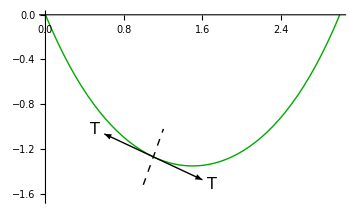

The force will be acting along the rope. It can be proven that, if the rope has no stiffness, any lateral stresses would cause it to twist or bend.

We can write the force that acts on the left section of the rope as T  l^–, where l^– is the unit vector pointing along the cable in the +x direction and T is the magnitude of tension at that point of the rope. Similarly, the force with which the right part of the cable is pulled by the left part is given as -T  l^–. Below is given an illustration of that:

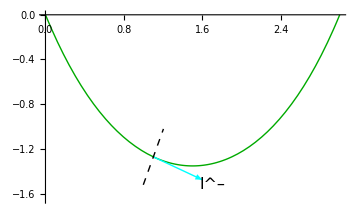

It is convenient to introduce a new vector T^–, which is defined as

T^– ≡ T l^–

The meaning of this vector is that if we divide the cable in two sections, the left side will experience a force T^– exerted by the right side, while the right side will feel a force -T^– from the left side.

It’s important to remember that it’s not completely valid to think of the tension force as a vector, as it acts in both sides; in reality, the force of tension is most correctly described by the stress tensor, which in this case happens to take a diagonal form.

#### Total tension force acting on a small piece of rope

Let’s look at a small piece of cable confined between x_0 and x_0 + dx, where dx is some small number. The force of tension acts on it from both sides:

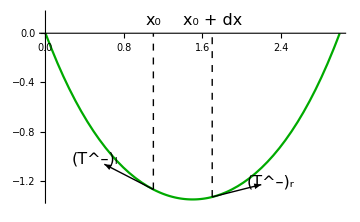
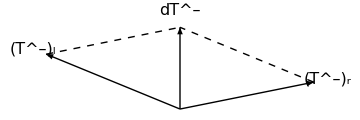

The total force that the rest of the rope exerts on this section equals (T^–)_l + (T^–)_r. We know that (T^–)_l = -T^–[t, x_0] ,   (T^–)_r = T^–[t, x + dx_0]. Since dx is very small, we can say that (T^–)_l + (T^–)_r = T^–[t, x_0 + dx] - T^–[t, x_0]= (∂T^–)/(∂x)dx. So, the total force is given as follows.

d T^– = (∂T^–)/(∂x)dx

We can show that this formula holds for arbitrary parametrization of the rope’s shape:

d T^– = (∂T^–)/(∂α)dα

What this means is that instead of describing the rope’s shape as y[x] and z[x], we could use some other parameter α (for example, arc length) and parametrize the shape of the cable as x[α], y[α], z[α]. And if we take a small piece of rope between α = α_0 and α = α_0 + dα, we could find the total force of tension acting on it using (9).

#### Code used to generate the visualizations

```mathematica
With[{x0 = 1.1},
	Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Arrow[{#, # - 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Thick, Arrow[{#, # + 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Text[Style["T", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} - 0.6{1, Sinh[x0 - 1.5]}]},
				{Text[Style["T", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 - 1.5]}]},
				{Dashed, Line[{# + 0.25{Sinh[x0 - 1.5], -1}, # - 0.25{Sinh[x0 - 1.5], -1}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5] - 0.3, 0}},
		ImageSize -> Medium
	]
]
```

-Graphics-

```mathematica
With[{x0 =1.1},
	Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Cyan, Arrow[{#, # + 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Text[Style["l^–", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 - 1.5]}]},
				{Dashed, Line[{# + 0.25{Sinh[x0 - 1.5], -1}, # - 0.25{Sinh[x0 - 1.5], -1}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5] - 0.3, 0}},
		ImageSize -> Medium
	]
]
```

-Graphics-

```mathematica
With[{x0 = 1.1, dx = 0.6},
	Row[{Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Arrow[{#, # - 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Thick, Arrow[{#, # + 0.5{1, Sinh[x0 + dx - 1.5]}}& @ {x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]}]},
				{Dashed, Line[{{x0, Cosh[x0 - 1.5] - Cosh[1.5]}, {x0, 0}}]},
				{Dashed, Line[{{x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]}, {x0 + dx, 0}}]},
				{Text[Style["x_0", 16], {x0, 0.1}]},
				{Text[Style["x_0 + dx", 16], {x0 + dx, 0.1}]},
				{Text[Style["(T^–)_l", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} - 0.6{1, Sinh[x0 - 1.5]}]},
				{Text[Style["(T^–)_r", 16], {x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 + dx - 1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5], 0.15}},
		ImageSize -> Medium
	],
	Graphics[{
		{Thick, Arrow[{{0, 0}, -0.5{1, Sinh[x0 - 1.5]}}]}, {Text[Style["(T^–)_l", 16], -0.55{1, Sinh[x0 - 1.5]}]},
		{Thick, Arrow[{{0, 0}, 0.5{1, Sinh[x0 + dx - 1.5]}}]}, {Text[Style["(T^–)_r", 16], 0.55{1, Sinh[x0 + dx - 1.5]}]},
		{Arrow[{{0, 0}, 0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]}, {Text[Style["dT^–", 16], 0.6{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}]},
		{Dashed, Line[{-0.5{1, Sinh[x0 - 1.5]}, 0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]},
		{Dashed, Line[{0.5{1, Sinh[x0 + dx - 1.5]}, 0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]}
	}, ImageSize -> Medium]
	}]
]
```

-Graphics--Graphics-

### Unit tangent vector expressed in the coordinates ζ, y, h

Let’s say there is a point with coordinates <ζ,y, h[ζ]> that lies on the cable. Now, let’s change ζ by some small value dζ, so that we are now at the point <ζ + dζ, y[ζ + dζ], h[ζ + dζ]>. By chain rule, the displacement vector is given as d r^– = ((∂r^–)/(∂ζ) + (∂r^–)/(∂y)(∂y)/(∂ζ) + (∂r^–)/(∂h)(∂h)/(∂ζ))dζ; by the definition of ζ^̑, y^̑, and h^̑ (6), this equals

δ r^– = ((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r)dζ

where (ζ^̑)_r[t, ζ] ≡ ζ^̑[ζ, y[t, ζ], h[t, ζ]], and the same is true for (y^̑)_r and (h^̑)_r. We can get the unit tangent vector by normalizing the displacement vector: l^– = (d r^–)/(√(dr^– · d r^–)). Using formulas (7), (8), (9), we get

l^– = ((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r)/(√(f_r^2 + ((∂y)/(∂ζ))^2 + ((∂h)/(∂ζ))^2))

Strictly speaking, -l^– would also be a unit tangent vector. But from the two possible options, let’s choose the vector l^– given by (30), as it points to the +x direction. Now, because the cable is oscillating and bending, l^– would be a function of time as well as position: l^– = l^–[t, ζ]. There is no y or h in the arguments because l^– is only defined along the rope, and so y and h are determined by ζ. In other words, if we know that a point lies on the rope and we are given its ζ coordinate, we know that its coordinates y and h are given as y[t, ζ] and h[t, ζ], respectively.

## Deriving the equations of motion

### Writing the Newton’s second law

Let’s write the Newton’s second law for a small section A of the rope confined between the points with coordinates ζ_A and ζ_A + dζ.

dm (d(v^–)_A)/dt = ∑F^–

Here dm is the mass of the small piece of rope A, (v^–)_A is its velocity vector, and ∑F^– is the total force acting on it. According to (22), the length of the piece of rope is given as dl = f_r dζ. The mass of the section equals δm = ρ dl = ρ f_r δζ. As we saw earlier, there are three forces acting on this body: the force of gravity (F^–)_g, the force of tension from the left (T^–)_l, and the force of tension from the right (T^–)_r. Substituting (29) and (F^–)_g = g^–  dm, we get that ∑F^– = g^– dm + (∂T^–)/(∂ζ)dζ.

ρ f_r (d(v^–)_A)/dt = (∂T^–)/(∂ζ) + ρ f g^–

The velocity vector v^– of the small segment is by definition (v^–)_A = (d(r^–)_A)/dt. By chain rule, (d(r^–)_A)/dt = (∂r^–)/(∂ζ)dζ_A/dt + (∂r^–)/(∂y)dy_A/dt + (∂r^–)/(∂h)dh_A/dt, where ζ_A, y_A, h_A are the coordinates of the small section A and all the derivatives are evaluated at <ζ_A, y_A, h_A>. Using the definition of the basis vectors (6), this can be written as (v^–)_A = (ζ^̑)_A dζ_A/dt + (y^̑)_A dy_A/dt + (h^̑)_A dh_A/dt, where (ζ^̑)_A[t] ≡ ζ^̑[ζ_A[t], y_A[t], h_A[t]] is the value of ζ^̑ at the point <ζ_A, y_A, h_A>, and the same goes for (y^̑)_A and (h^̑)_A. We can take the time derivative of this quantity using the product rule:

(d (v^–)_A)/dt = (ζ^̑)_A(d^2 ζ_A)/dt^2 + (y^̑)_A(d^2 y_A)/dt^2 + (h^̑)_A(d^2 h_A)/dt^2 + (d(ζ^̑)_A)/dt dζ_A/dt + (d(y^̑)_A)/dt dy_A/dt + (d(h^̑)_A)/dt dh_A/dt

Since the basis vectors  are functions of position, their derivatives can be found using the chain rule. For (ζ^̑)_A[t] ≡ ζ^̑[ζ_A[t], y_A[t], h_A[t]], for example, we have (d(ζ^̑)_A)/dt = (∂ζ^̑)/(∂ζ)dζ_A/dt + (∂ζ^̑)/(∂y)dy_A/dt + (∂ζ^̑)/(∂h)dh_A/dt, where (∂ζ^̑)/(∂ζ), (∂ζ^̑)/(∂y), (∂ζ^̑)/(∂h) are evaluated at <ζ_A, y_A, h_A>. We can see that the time derivatives of the basis vectors are of order ε. Thus, when multiplied by the time derivatives of the coordinates ζ_A, y_A, h_A in (32), which are themselves of order ε, they would produce quadratic terms that we would neglect:

(d (v^–)_A)/dt = (ζ^̑)_A(d^2 ζ_A)/dt^2 + (y^̑)_A(d^2 y_A)/dt^2 + (h^̑)_A(d^2 h_A)/dt^2 + O[ε^2]

Using the definition u_A  ≡ dζ_A/dt (24) and substituting the formula into (31) yields

ρ f_r((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) = (∂T^–)/(∂ζ) + ρ f_r g^–

Because ((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) is of order ε, we only need the zeroth order term in the Taylor expansion of f_r, which equals 1 (9).

ρ ((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) = (∂T^–)/(∂ζ) + ρ f_r g^–

### Writing the equations

To derive the equations of motion, we shall combine Newton’s second law (33), the incompressibility condition (26), the condition that there are no lateral stresses (28), the formula for the cable’s equilibrium shape (1), and the geometrical identities (10)-(21). We also neglect the O[ε^2] terms quadratic in the cable’s displacement. The derivation is quite long and is given in the full version of the work in the chapters “Curvilinear coordinates” and “Introducing small oscillations”. Here, we can just write the equations of motion:

(∂^2 ψ)/(∂τ^2) = ∂/(∂σ)[√(1+σ^2)(∂ψ)/(∂σ)]

∂^2/(∂τ^2)[(1+2 σ^2)/(1+σ^2)η + 4 σ(∂η)/(∂σ) + (1+σ^2)(∂^2 η)/(∂σ^2)] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

Here, τ, σ, ψ, η are dimensionless variables which are defined as

σ  ≡  (ζ - l_0)/Λ = Sinh[(x - x_0)/Λ]
τ  ≡  t / √(Λ/g)
ψ ≡ y / Λ
η ≡ h / Λ

### Formulating the boundary conditions

The cable’s ends are fixed. Mathematically, we can formulate it as

y[t, 0] = y[t, L] = 0
h[t, 0] = h[t, L] = 0

u[t, 0] = u[t, L] = 0

What (37) says is that the cable passes through the points O and P. The equation (38) says that at the points O and P, the cable’s tangential velocity is zero. By plugging in (36), we can see that in terms of the dimensionless variables ψ the boundary condition for ψ (37) can be written as

ψ[τ, σ_0] = 0
ψ[τ, σ_p] = 0

where σ_0 and σ_p are the coordinates σ of the points O and P, respectively. For η, we also have η[τ, σ_0] = h[τ, σ_p] = 0. And although it might not be immediately obvious, the condition (38) can actually be written in terms of η using Newton’s second law, as shown in the full version of the work.

η[τ, σ_0] = 0
η[τ, σ_p] = 0
∂^2/(∂^2 τ)(∂η)/(∂σ) = √(1+σ^2)(∂^3 η)/(∂σ^3) + (4 σ)/(√(1+σ^2))(∂^2 η)/(∂σ^2) + (3+2 σ^2)/((1+σ^2)^(3/2))(∂η)/(∂σ)               σ = σ_0 || σ = σ_p

## Nonlocality of in-plane oscillations

Notice that the left-hand-side of (35) is not just ∂^2 η/∂τ^2 but also contains its spacial derivatives, as can be seen from the equation below, which is another way to write (35). Knowing the spacial derivatives of h at a particular point is not enough to tell what ∂^2 η/∂τ^2 is, as you would also have to know ∂/(∂σ)(∂^2 η/∂τ^2) and (∂^2 /∂σ^2)(∂^2 η/∂τ^2). To find ∂^2 η/∂τ^2, you would have to use boundary conditions and integrate. Physically, this means that looking at a small section of the cable is not enough to determine its acceleration, and the system is, in some sense, nonlocal.

{(1+2 σ^2)/(1+σ^2) + 4 σ∂/(∂σ) + (1+σ^2)∂^2/(∂σ^2)}(∂^2 η)/(∂τ^2) = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

As a simple example, consider the following initial conditions. At time zero, η is zero everywhere except for a small region. Then, the right-hand side of (35) vanishes everywhere except that small region. But because the left-hand-side of (35) is effectively an ODE with σ as the independent variable and ∂^2 η/∂τ^2 as the dependent variable, even if the right-hand side is nonzero only in a small region, ∂^2 η/∂τ^2 is generally nonzero outside of this region. In other words, by displacing a small piece of cable, we can immediately set the entire system in motion. Effectively this means that signals can travel immediately across the cable, or, in other words, the speed of sound is infinite - at least in the approximations used.
	And it’s important to keep in mind that (35) is only approximate. While deriving it, we regarded the cable as incompressible, which is impossible in real life - special relativity, for example, dictates that there can be no absolutely rigid bodies or unstretchable cables precisely because this would violate the postulate that information cannot travel faster than light. Infinite speed of sound in (35) is also impossible in Newton’s mechanics, as the cable is elastic and hence stretches and compresses slightly under axial stresses. And this is this deformation that makes the speed of sound finite.
	The equation (35) is a good model for oscillations whose characteristic wavelength is of the same order of magnitude  as the cable’s curvature. High-wavelength oscillations have a frequency much less than the cable’s length divided by the speed of sound in steel (the “ordinary” speed of sound √(E/ρ)), and so the deformation is not significant. Taking a small piece of cable and moving it involves high-frequency modes (for intuition, consider the Fourier series of η[0, σ] - sharp distortions inevitably bring high harmonics), so it is outside the range of applicability of (35). But if we restrain ourselves to low-frequency oscillations only, we see that we can only displace the cable in a “smooth” way, meaning that the characteristic wavelength of the displacement must be of the same order as the cable’s radius of curvature, so infinite speed of signal propagation is not an issue because of the restriction to only deal with small frequency modes effectively forbade us from looking at the propagation of information in the first place - with low-frequency modes, we can only construct oscillations that have already “reached everywhere on the cable”.

## Finding the normal modes of horizontal motion

### Writing the normal mode equation for ψ

The equation (34) reads

(∂^2 ψ)/(∂τ^2) = √(1+σ^2)(∂^2 ψ)/(∂σ^2) + σ/(√(1+σ^2))(∂ψ)/(∂σ)

Since it’s a linear equation, its solution is a sum of its normal modes:

ψ[τ, σ] = (∑^∞)_(n = 1)C_n ψ_n[σ] Cos[ϖ_n τ + ϕ_n]

where each of the C_n and ϕ_n is a constant determined by the initial conditions, ψ_n and ϖ_n describe the n-th normal mode of the equation. Substituting this into the equation (34) and using the fact that the normal modes ψ_n are linearly independent, we get

√(1+σ^2)(d^2 ψ_n)/dσ^2 + σ/(√(1+σ^2))dψ_n/dσ + ϖ_n^2 ψ_n = 0

### Solving the normal mode equation using Frobenius’s method

In terms of the new variable ξ ≡ √(1 + σ^2) - 1 (idea from John Gregg Gale's master's thesis, 1976), for positive σ, the equation (42) becomes

(1 + ξ)(ϖ^2 ψ + dψ/dξ) + ξ(2 + ξ) (d^2 ψ)/dξ^2 = 0

This is a homogenous linear ODE with polynomial coefficients, so it can be solved using the Frobenius’s method near the singular point ξ = 0. The two linearly-independent solutions of (43) are

ψ_((frob)0)[ϖ, ξ] = 1 - ξ ϖ^2 + (ξ^2 ϖ^4)/6 + ...
ψ_((frob)1/2)[ϖ, ξ] = √ξ - 1/12 (1 + 4 ϖ^2)ξ^(3/2) + ...

After finding ψ[ξ], we can find ψ[σ] by substituting ξ = √(1 + σ^2) - 1. Now, since when deriving (43) we assumed that σ was positive but we are also interested in the region σ < 0, we now need to use parity to “extend” the solutions we got for σ > 0. The point where the regions σ ≥ 0 and σ ≤ 0 meet is σ = 0; for σ → 0, we have ξ = √(1 + σ^2) - 1 = σ^2/2 + O[σ^4]. Leaving only the terms with the smallest powers of σ, we get

ψ_((frob)0) = 1 - ϖ^2 σ^2/2 + O[σ^4]
ψ_((frob)1/2)  = σ/(√2) + O[σ^3]

Now, notice that ψ_0 has its derivative zero at σ = 0, while ψ_(1/2) is itself zero. Because of the reflection symmetry of the equation (42) around σ = 0 and the condition that the function ψ[σ] and its first derivative must be continuous, this means that the extension of ψ_((frob)0) is an even function, while that of ψ_((frob)1/2) - an odd function.

ψ_0[ϖ, σ] =ψ_((frob)0)[ϖ, √(1 + σ^2) - 1]
ψ_1[ϖ, σ] = √2 Sign[σ]ψ_((frob)1/2)[ϖ, √(1 + σ^2) - 1]

where ψ_((frob)0)[ξ] and ψ_((frob)1/2)[ξ] are given by (44). The functions ψ_0[σ] and ψ_1[σ] are constructed so that ψ_0[0] = 1, d/dσ ψ_0[0]= 0 and ψ_1[0] = 0, d/dσ ψ_1[0] = 1. Having found two linearly independent solutions, we can find the general solution to (42) as their superposition:

ψ_n[σ] = C_0 ψ_0[ϖ_n, σ] + C_1 ψ_1[ϖ_n, σ]

Here n labels a normal mode and goes from 1 to ∞. In this context, ψ_1[σ] (46 with n = 1) must be distinguished from ψ_1[ϖ, σ] (45). While ψ_1[σ] is a normal mode of (34) with a given value of the parameter ϖ that satisfies the boundary conditions, ψ_1[ϖ, σ] is an auxiliary function; these two can be differentiated using the fact that ψ_1 the normal mode has one argument, σ, while ψ_1 the auxiliary function has two arguments, ϖ and σ. Of course, Frobenius’s method only gives solutions with a finite radius of convergence, so if σ_0 or σ_p is too large, the functions ψ_0 and ψ_1 in (46) have to be found numerically.

### Finding the equation determining the normal frequencies

The formula (46) gives us the general solution of (42). It contains two arbitrary constants C_0 and C_1, whose values must be such that the boundary conditions (39) are satisfied. Substituting (46) into (39), we get a system of equations that can be written in matrix form as

(ψ_0[ϖ, σ_0] | ψ_1[ϖ, σ_0]
ψ_0[ϖ, σ_1] | ψ_1[ϖ, σ_1])(C_0
C_1) = 0

This equation only has nonzero solutions C_0, C_1 when the determinant of the matrix is zero. Denoting it as Ψ[ϖ, σ_0, σ_p], we get that for ψ_n[σ] to be nonzero, the determinant of Ψ must be zero:

Ψ[ϖ, σ_0, σ_p] ≡ (ψ_0[ϖ, σ_0] | ψ_1[ϖ, σ_0]
ψ_0[ϖ, σ_1] | ψ_1[ϖ, σ_1])
det Ψ[ϖ_n, σ_0, σ_p] = 0

where ϖ_n is proportional to the n-th normal frequency. Here ψ_0[ϖ, σ] is given by (45). The equation (48) only holds for certain values of ϖ; this is a mathematical formulation of the fact that only some values of ϖ are allowed for normal modes, while some are not. In fact, we can use the equation to find the normal frequencies of our system. In the plot below, you can see that det Ψ = 0 for some specific values of ϖ. In the figure below, you can see the plot of det Ψ as a function of ϖ for σ_0 = -1, σ_p = 1.

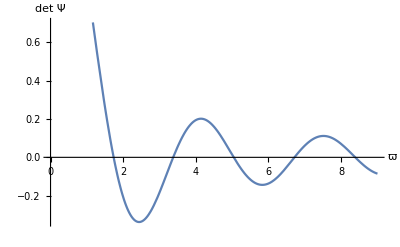

As it is shown in the full version, det Η[0, σ_0, σ_p] is never  zero for σ_0 ≠ σ_p.

## Finding the normal modes of in-plane motion

### Writing the normal mode equation for η

The equation (35) reads

∂^2/(∂τ^2)[(1+2 σ^2)/(1+σ^2)η + 4 σ(∂η)/(∂σ) + (1+σ^2)(∂^2 η)/(∂σ^2)] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

Since it’s a linear equation, its solution is a sum of its normal modes:

η[τ, σ] = (∑^∞)_(n = 1)C_n η_n[σ] Cos[ϖ_n τ + ϕ_n]

where each of the C_n and ϕ_n is a constant determined by the initial conditions, η_n and ϖ_n describe the n-th normal mode of the equation. Substituting this into the equation (35) and using the fact that the normal modes η_n are linearly independent, we get

(1+σ^2)^(3/2)(d^4 η_n)/dσ^4 + 7 σ √(1+σ^2)(d^3 η_n)/dσ^3 + (ϖ_n^2(1+σ^2) + (7+10 σ^2)/(√(1+σ^2)))(d^2 η_n)/dσ^2+ (4 ϖ_n^2 σ - (σ (1-2 σ^2))/((1+σ^2)^(3/2)))dη_n/dσ + (ϖ_n^2(1+2 σ^2)/(1+σ^2) - (2 (1-2 σ^2))/((1+σ^2)^(5/2)))η_n = 0

### Solving the normal mode equation using Frobenius’s method

In exactly the same way as with horizontal normal modes, the equation (50) can be re-written in terms of ξ ≡ √(1 + σ^2) - 1 (idea from John Gregg Gale’s master’s thesis, 1976). The resulting equation can be solved using Frobenius’s method near the singular point ξ = 0:

η_((frob)0)[ϖ, ξ] = 1-1/6 ξ^2 (-2+ϖ^2)+1/90 ξ^3 (-36+5 ϖ^2+ϖ^4) + ...
η_((frob)1/2)[ϖ, ξ] = ξ^(1/2) +1/480 ξ^(5/2) (111-68 ϖ^2)+(ξ^(7/2) (-6039+1294 ϖ^2+136 ϖ^4))/20160 + ...
η_((frob)1)[ϖ, ξ] = ξ-1/6 ξ^2 (4+ϖ^2)+1/90 ξ^3 (54+5 ϖ^2+ϖ^4) + ...
η_((frob)3/2)[ϖ, ξ] = ξ^(3/2)-1/20 ξ^(5/2) (13+2 ϖ^2)+(ξ^(7/2) (1843+92 ϖ^2+16 ϖ^4))/3360

After finding η[ξ], we can find η[σ] by substituting ξ = √(1 + σ^2) - 1. Now, since when deriving the ξ-version of (50) we assumed that σ was positive, but we are also interested in the region σ < 0, we now need to use parity to “extend” the solutions we got for σ > 0. The point where the regions σ ≥ 0 and σ ≤ 0 meet is σ = 0; for σ → 0, we have ξ = √(1 + σ^2) - 1 = σ^2/2 + O[σ^4]. Leaving only the terms with the smallest powers of σ, we get

η_((frob)0) = 1 + O[σ^4]
η_((frob)1/2)  = σ/(√2) + O[σ^4]
η_((frob)1) = σ^2/2 + O[σ^4]
η_((frob)3/2) = σ^3/(2 √2) + O[σ^4]

Now, notice that the functions only have either their value or one of the first three derivatives nonzero at σ → 0^+. Because of the reflection symmetry of the equation (50) around σ = 0 and the condition that the function η[σ] and its first three derivatives must be continuous, this means that the extensions of η_((frob)0) and η_((frob)1) are even functions, while that of ψ_((frob)1/2) and ψ_((frob)3/2) - odd functions.

η_0[ϖ, σ] =η_((frob)0)[√(1 + σ^2) - 1]
η_1[ϖ, σ] = √2 Sign[σ]η_((frob)1/2)[√(1 + σ^2) - 1]
η_2[ϖ, σ] =η_((frob)1)[√(1 + σ^2) - 1]
η_3[ϖ, σ] = (√2)/3 Sign[σ]η_((frob)3/2)[√(1 + σ^2) - 1]

where η_((frob)0)[ϖ, ξ], η_((frob)1/2)[ϖ, ξ], η_((frob)1)[ϖ, ξ], η_((frob)3/2)[ϖ, ξ] are given by (51). The functions η_0[ϖ, σ], η_1[ϖ, σ], η_2[ϖ, σ], η_3[ϖ, σ] are constructed so that d^p/dσ^p η_(m,p)[0] = δ_mp. A general solution to (50) is given by

η_n[σ] = C_0 η_0[ϖ_n, σ] + C_1 η_1[ϖ_n, σ] + C_2 η_2[ϖ_n, σ] + C_3 η_3[ϖ_n, σ]

Here n labels a normal mode and goes from 1 to ∞. In this context, η_1[σ] (53 with n = 1) must be distinguished from η_1[ϖ, σ] (52). While η_1[σ] is a normal mode of (35) with a given value of the parameter ϖ that satisfies the boundary conditions, η_1[ϖ, σ] is an auxiliary function; these two can be differentiated using the fact that η_1 the normal mode has one argument, σ, while η_1 the auxiliary function has two arguments, ϖ and σ.

### Finding the equation determining the normal frequencies

The formula (53) gives us the general solution of (50). It contains four arbitrary constants C_0, C_1, C_2, C_3, whose values must be such that the boundary conditions (40) are satisfied. Substituting (53) into (40), we get a system of equations that can be written in a matrix form as

(η_0[ϖ, σ_0] | η_1[ϖ, σ_0] | η_2[ϖ, σ_0] | η_3[ϖ, σ_0]
η_0[ϖ, σ_p] | η_1[ϖ, σ_p] | η_2[ϖ, σ_p] | η_3[ϖ, σ_p]
(B^̑)_ϖ η_0[σ_0] | (B^̑)_ϖ η_1[σ_0] | (B^̑)_ϖ η_2[σ_0] | (B^̑)_ϖ η_3[σ_0]
(B^̑)_ϖ η_0[σ_p] | (B^̑)_ϖ η_1[σ_p] | (B^̑)_ϖ η_2[σ_p] | (B^̑)_ϖ η_3[σ_p])(C_1
C_2
C_3
C_4) = 0
(B^̑)_ϖ η ≡ √(1+σ^2)(∂^3 η)/(∂σ^3) + (4 σ)/(√(1+σ^2))(∂^2 η)/(∂σ^2) + ((3+2 σ^2)/((1+σ^2)^(3/2)) + ϖ^2)(∂η)/(∂σ)

As in the case of horizontal oscillations, this equation will only have nonzero solutions C_0, C_1, C_2, C_3 and lead to a nonzero normal mode η_n if the determinant of the matrix is zero:

Η[ϖ, σ_0, σ_p] ≡ (η_0[ϖ, σ_0] | η_1[ϖ, σ_0] | η_2[ϖ, σ_0] | η_3[ϖ, σ_0]
η_0[ϖ, σ_p] | η_1[ϖ, σ_p] | η_2[ϖ, σ_p] | η_3[ϖ, σ_p]
(B^̑)_ϖ η_0[σ_0] | (B^̑)_ϖ η_1[σ_0] | (B^̑)_ϖ η_2[σ_0] | (B^̑)_ϖ η_3[σ_0]
(B^̑)_ϖ η_0[σ_p] | (B^̑)_ϖ η_1[σ_p] | (B^̑)_ϖ η_2[σ_p] | (B^̑)_ϖ η_3[σ_p])
det Η[ϖ_n, σ_0, σ_p] = 0

The equation (55) only holds for certain values of ϖ; this is a mathematical formulation of the fact that only some values of ϖ are allowed for normal modes, while some are not. In fact, we can use the equation to find the normal frequencies of our system. Below you can see the plot of det Η as a function of ϖ for σ_0 = -1, σ_p = 1; you can see that det Η is only zero for some specific values of ϖ.

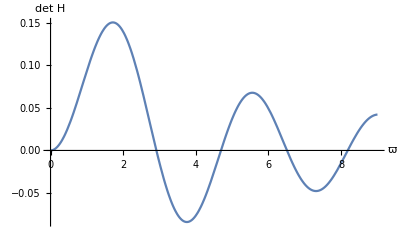

As it is shown in the full version, ϖ cannot be zero. Even though det Η[0, σ_0, σ_p] = 0 for all σ_0 and σ_p, ϖ = 0 is impossible because of conservation of length (see the full version).

## Approximate algebraic expression for the natural frequencies and normal modes that gets more accurate as the mode number increases or the cable becomes tighter

### Approximate formula for the normal modes

For a straight wire, we know that the normal modes of horizontal oscillations are precisely ψ[σ] = A Sin[κ(σ - σ_0)], where A is an arbitrary constant and κ = π/(σ_p - σ_0)n for n ∈ ℕ; for high n, κ becomes large as well. From physical intuition, we would expect to see something similar in a sagging cable. Given a normal mode of the equation (34), we can always write it in the form ψ[σ] = A[σ] Sin[ϕ[σ]]. And in fact, there are infinitely many ways to do that - take, for example, A[σ] = ψ[σ]/Sin[C], ϕ[σ] = C, where C can be any nonzero number. But let’s pick A and ϕ such that A ≈ const, dϕ/dσ ≈ const; this would be a mathematical statement of the fact that we are looking for a near-sinusoidal solution ψ[σ] ≈ C_1 Sin[C_2 σ]. The quantity dϕ/dσ will be very important in the calculations, so let us denote dϕ/dσ[σ] ≡ κ[σ]. For high-frequency modes, the phase changes very rapidly with position, so κ[σ] >> 1. Following the intuition from a tight string, high frequency normal modes correspond to the limit κ[σ] → ∞.
	Substituting ψ[σ] = A[σ] Sin[ϕ[σ]], we arrive at the following equation. Here k[σ] ≡ dϕ/dσ[σ].

(ϖ^2/κ^2 - √(1+σ^2)) κ^2 A Sin[ϕ] + (σ/(√(1+σ^2))κ A + 2 √(1+σ^2)  κ dA/dσ +√(1+σ^2)dκ/dσ A) Cos[ϕ] + (σ/(√(1+σ^2)) dA/dσ+√(1+σ^2)(d^2 A)/dσ^2)Sin[ϕ] = 0

The first term is of order κ^2, so it is much larger than the second term, which is of order κ, which is in turn much larger than the third term, which as no factors of κ in it. Since we are looking for an approximate solution for κ >> 1, we should first equate the first, potentially largest, term to zero. Although this would not give us a precise solution, it is a good approximation. The formula we get by equating the first two terms in (56) to zero is

ψ[σ] ≈ Sin[ϖ σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - ϕ_0]/((1+σ^2)^(1/8))
ϕ_0 ≡ ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]

where ϕ_0 = ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2] is determined by the boundary condition ψ[σ_0] = 0 (39). The formula makes (57) makes (56) hold up to the O[1] terms, which have no factors of κ in them. Because (56) was obtained from (42) (which is the equation for the normal modes of (34)) by substituting ψ[σ] = A[σ] Sin[ϕ[σ]], the error in (42) is the same as in (56). So, the above formula (57) makes the error in (42) a fixed number that doesn’t change as we increase ϖ. On the other hand, looking at the equation √(1+σ^2)(d^2 ψ)/dσ^2 + σ/(√(1+σ^2))dψ/dσ + ϖ^2 ψ = 0, it is clear that as κ and ϖ get larger, a fixed error in ψ would result in an increasingly large error. And since we know that the error in (42) when substituting (57) is fixed, we conclude that (57) approaches the exact solution to (42) as ϖ → ∞.
	We can repeat the same procedure with in-plane oscillations; their normal modes are given by the equation (50). Miraculously, doing so gives the same answer as what we got for horizontal oscillations:

η[σ] ≈ Sin[ϖ σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - ϕ_0]/((1+σ^2)^(1/8))
ϕ_0 ≡ ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]

An intuitive explanation for why the normal modes for horizontal and in-plane motion are the same for large ϖ is that the cable’s curvature radius becomes much larger than the normal modes’ characteristic length, which means that the cable can be treated as “locally flat”. And for a flat cable, the normal modes of horizontal and in-plane motion are of course the same.

### Estimating the normal frequencies

We saw that for high ϖ, the normal modes of both (34) and (35) can be approximated as

ψ[σ] ≈ η[σ] ≈ Sin[ϖ σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - ϕ_0]/((1+σ^2)^(1/8))
ϕ_0 ≡ ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]

On the other hand, we know that the cable’s right end is fixed, so ψ[σ_p] = η[σ_p] = 0. To satisfy this condition, the argument of the sine function must be a multiple of π:

ϖ_n (σ_p Hypergeometric2F1[1/4,1/2,3/2,-σ_p^2] - σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]) = n π

This gives us an estimate for the n’th natural frequency of the system for n >> 1:

ϖ_n ≈ π/(σ_p Hypergeometric2F1[1/4,1/2,3/2,-σ_p^2] - σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2])n

The expression tells us that for large n, the corresponding ϖ_n’s are evenly spaced.

## Orthogonality of the normal modes of (34)

The equation (42) reads

d/dσ[√(1+σ^2)dψ_n/dσ] + ϖ^2 ψ_n = 0

In terms of a new variable χ ≡ ArcSinh[σ], it can be written as

(d^2 ψ_n)/dχ^2 + ϖ_n^2 Cosh[χ]ψ_n = 0

Now, let us look at some two normal modes ψ_n and ψ_m.

(d^2 ψ_m)/dχ^2 + ϖ_m^2 Cosh[χ]ψ_m = 0
(d^2 ψ_n)/dχ^2 + ϖ_n^2 Cosh[χ]ψ_n = 0

Multiplying the first equation by ψ_n, the second one by ψ_m, and integrating, we obtain

(∫^χ_p)_χ_0 ψ_n(d^2 ψ_m)/dχ^2 dχ + ϖ_m^2(∫^χ_p)_χ_0 Cosh[χ]ψ_n ψ_m dχ = 0
(∫^χ_p)_χ_0 ψ_m(d^2 ψ_n)/dχ^2 dχ + ϖ_n^2(∫^χ_p)_χ_0 Cosh[χ]ψ_m ψ_n dχ = 0

where χ_0 ≡ ArcSinh[σ_0], χ_p ≡ ArcSinh[σ_p] are the coordinates χ of the cable’s edges. Now, notice that the second term is the same in both equations, so we have

(ϖ_m^2 - ϖ_n^2)(∫^χ_p)_χ_0 Cosh[χ]ψ_n ψ_m dχ = (∫^χ_p)_χ_0 ψ_m(d^2 ψ_n)/dχ^2 dχ - (∫^χ_p)_χ_0 ψ_n(d^2 ψ_m)/dχ^2 dχ

Using integration by parts and the boundary conditions ψ[χ_0] = ψ[χ_p] = 0, we can show that the right-hand side is zero. If we are talking about two normal modes with different ϖ’s, then the coefficient ϖ_m^2 - ϖ_n^2 is nonzero, and the only way to satisfy the equality is to make the integral itself zero:

(∫^χ_p)_χ_0 ψ_n ψ_m Cosh[χ]dχ = 0                    ϖ_n ≠ ϖ_m

Now, notice that Cosh[χ] dχ is nothing but d Sinh[χ]. Since χ is defined as χ ≡ ArcSinh[σ], we have d Sinh[ArcSinh[σ]] = dσ. Changing variable of integration back to σ again, we obtain

(∫^σ_p)_σ_0 ψ_n[σ]ψ_m[σ]dσ = 0                    ϖ_n ≠ ϖ_m

Which means that any two normal modes of (89) with different ϖ’s are orthogonal. To illustrate that, let us compute the first six normal modes of (89) with σ_0 = -1, σ_p = 1, and compute (∫^σ_p)_σ_0 ψ_n[σ]ψ_m[σ]dσ for various m and n.

## Lax cable

Let’s say we take our cable and hang it from two points that are very close to each other. Intuitively, we would expect that as we bring the cable’s ends closer together, it would become more and more similar to a vertical line. In the figures below, you can see how a cable of length 1 would look like when hung from two points located at the horizontal distance of 0.4, 0.2, 0.1 from each other, respectively; you can see that the cable’s equilibrium shape indeed approaches a vertical line.

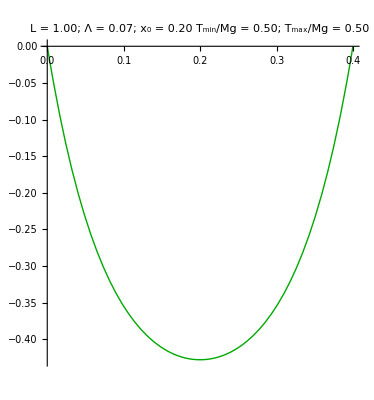
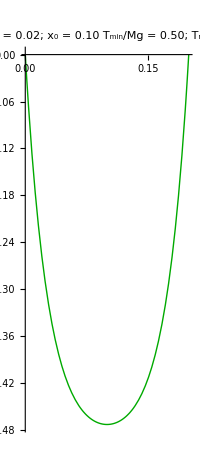
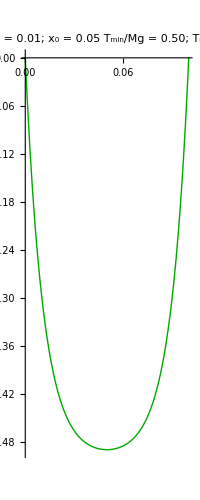

Intuitively, if in equilibrium a cable hangs almost vertically, then it’s also going to oscillate like a cable that, well, is hung vertically, as in this 2018 UCONN paper. Let us try to quantify this hypothesis.

The equations (42) and (50) determining the cable’s normal modes are written as

√(1+σ^2)(d^2 ψ)/dσ^2 + σ/(√(1+σ^2))dψ/dσ + ϖ^2 ψ = 0
(1+σ^2)^(3/2)(d^4 η)/dσ^4 + 7 σ √(1+σ^2)(d^3 η)/dσ^3 + (ϖ^2(1+σ^2) + (7+10 σ^2)/(√(1+σ^2)))(d^2 η)/dσ^2+ (4 ϖ^2 σ - (σ (1-2 σ^2))/((1+σ^2)^(3/2)))dη/dσ + (ϖ^2(1+2 σ^2)/(1+σ^2) - (2 (1-2 σ^2))/((1+σ^2)^(5/2)))η = 0

Here σ goes from -S to S, where S ≡ L/2Λ. Let us introduce a new variable ϛ ≡ σ/S, such that σ = S ϛ; this is convenient because now we have -1 ≤ ϛ ≤ 1. For derivatives, we have d/dσ = 1/S d/dϛ. By plugging in σ ≡ (ζ - l_0)/Λ (36) into the definition of ϛ, we can see that ϛ ≡ σ/S =  (ζ - l_0)/Λ/L/(2Λ), which is (ζ - l_0)/(L/2). So, ϛ is basically like ζ, except for a constant factor. The two equations can be written in terms of ϛ as

√(1/S^2+ϛ^2)(d^2 ψ)/dϛ^2 + ϛ/(√(1/S^2+ϛ^2))dψ/dϛ + γ^2 ψ = 0
(1/S^2+ϛ^2)^(3/2)(d^4 η)/dϛ^4 + 7 ϛ √(1/S^2+ϛ^2)(d^3 η)/dϛ^3 + (γ^2(1/S^2+ϛ^2) + (7/S^2+10 ϛ^2)/(√(1/S^2+ϛ^2)))(d^2 η)/dϛ^2+ (4 γ^2 ϛ - (ϛ (1/S^2-2 ϛ^2))/((1/S^2+ϛ^2)^(3/2)))dη/dϛ + (γ^2(1/S^2+2 ϛ^2)/(1/S^2+ϛ^2) - (2 (1/S^2-2 ϛ^2))/(S^2(1/S^2+ϛ^2)^(5/2)))η = 0

where γ^2 ≡ S ϖ^2. For |ϛ| >> 1 / S, this can be written as

ϛ(d^2 ψ)/dϛ^2 + dψ/dϛ + γ^2 ψ = 0
d^2/dϛ^2[ϛ^2(ϛ(d^2 η)/dϛ^2 + dη/dϛ + γ^2 ψ)] = 0

Integrating the bottom equation twice, we get

ϛ^2(ϛ(d^2 η)/dϛ^2 + dη/dϛ + γ^2 η) = C_0 + C_1 ϛ

Thus, for an infinitely lax cable, the normal modes of both horizontal and in-plane motion are described by basically the same equation:

ϛ(d^2 ψ)/dϛ^2 + dψ/dϛ + γ^2 ψ = 0
ϛ(d^2 η)/dϛ^2 + dη/dϛ + γ^2 η = C_0/ϛ^2 + C_1/ϛ

This is a relatively simple equation that can be solved in terms of Bessel functions:

```mathematica
DSolve[ϛ ψ''[ϛ] + ψ'[ϛ] + γ^2 ψ[ϛ] == 0, ψ, ϛ]
```

{{ψ→Function[{ϛ},BesselJ[0,2 γ √ϛ] C[1]+2 BesselY[0,2 γ √ϛ] C[2]]}}

This is the same as  the equation (16) in the article "Oscillations of a hanging chain" (UCONN, 2018), which looked at the oscillations of a vertically hanging cable. Intuitively this makes sense: if we bring the cable’s ends closer together, then it starts hanging almost vertically, and since it hangs almost vertically, then it  oscillates almost like a vertically hanging cable. Sounds even a bit obvious when phrased like this.

## Dispersion and “continuous reflection”

A short qualitative note to finalize the discussion of normal modes. As we saw from the chapter, the normal frequencies are not equidistant, and there is no reason to expect they would be rational multiples of each other. What this means is that if we set the cable oscillating at some moment in time, it will not return to its original configuration in any finite time. This in turn means that a pulse once launched in the cable does not just bounce back and forth but instead changes shape - this is what we usually call dispersion.
	And as we know from the propagation of waves in homogenous media with a nonlinear dispersion relation, dispersion generally causes pulses to not only “deform” but to also start “radiating backwards”. There is no reason we would expect dispersion in our system to be special in this sense, so the pulses most likely do “reflect backwards” as they travel.
	We can empirically check these two conclusions by numerically solving the equations of motion. For the sake of example, let us look at the horizontal oscillations with the initial conditions ψ[0, σ] = ψ_0[σ], ∂/(∂τ)ψ[0, σ]  = 0 - this is what happens if we displace the cable from equilibrium and hold it in this position, and then release. Let us look at the case when σ_0 = -1, σ_p = 1 for ψ[0, σ] = Exp[-40 σ^2]. We can solve the initial value problem using the first 18 normal modes and dropping the higher modes. (see details in the full version, sections “Solving the initial value problem” and “Dispersion ans “continuous reflection””)

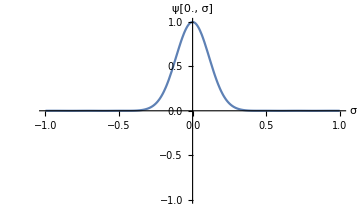
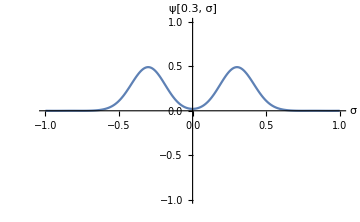
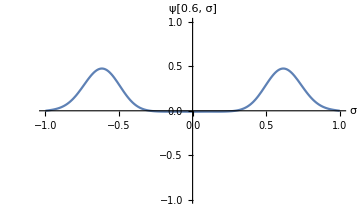
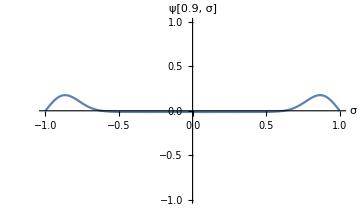
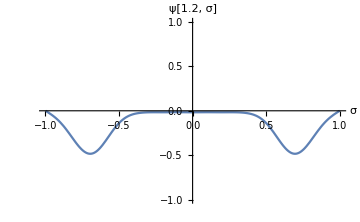
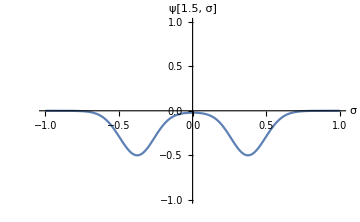
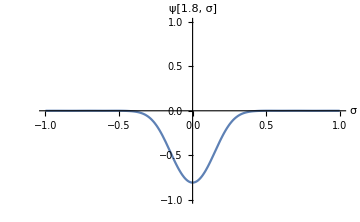

Notice that at first, the pulse just “bounces” back and forth as it would do in a tight string. However, after some time, it’s evident that its shape starts to change. After a few bounces, we see that the pulse leaves after itself not a region where ψ = 0, as for a tight string, but a region with some dissipated ψ:

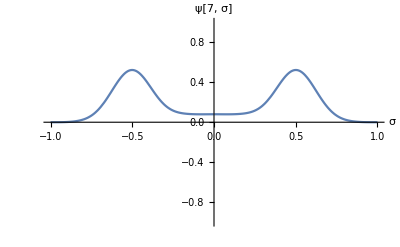

Below, you can see the plots of ψ[τ, σ] for τ = 100, 102, 104, 106, 108, 110. The shape of the original pulse has obviously been changed.

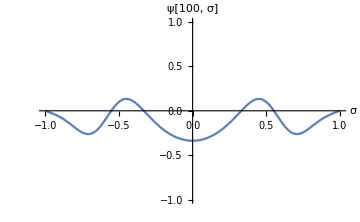
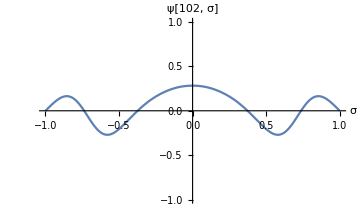
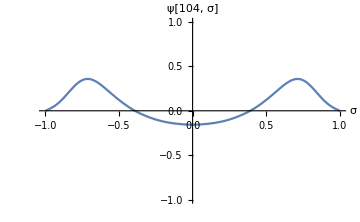
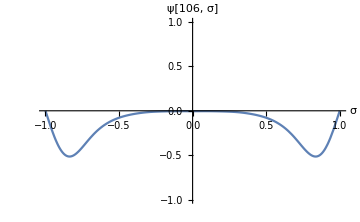
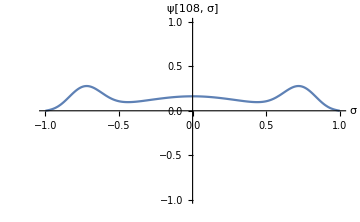
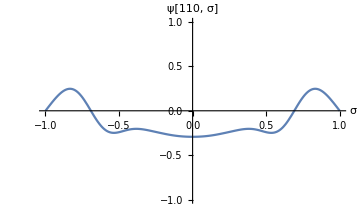

It is evident that the shape has changed a lot - so, we confirm the initial hypothesis that dispersion is present. In addition, we saw that even after a few bounces, the pulse leaves a “tail” - this illustrates the hypothesis about “continuous reflection”, which is due to the tension in the cable changing with position. We can break the cable into many infinitesimal tight strings with different tension, and in the interface of any two strings, there should be some reflection when a pulse passes - and this is indeed what we see. So far this is only numerical inexact argument, however, so the results should be taken with a grain of salt. There can be some numerical error due to the omission of high normal modes. The phenomenon is a very interesting thing to explore in further work.

## Oscillations of a discrete chain

## Kinematics of the chain

Imagine a system (later called chain) consisting of N+1 rigid massless rods each of length λ connected by frictionless joints to N+2 equal point masses m (later called balls), so that each rod is attached with joints to two balls without friction. Let us hold the two outmost balls - for example, attach them to a wall. How will the chain move under the influence of gravity?

### Numbering the balls and defining a coordinate system

First, let’s number the balls. Pick the two outmost balls and number them as 0 and N + 1, respectively. Now, number all the remaining balls such that they come in order. Below is an example of such numbering for N=12.

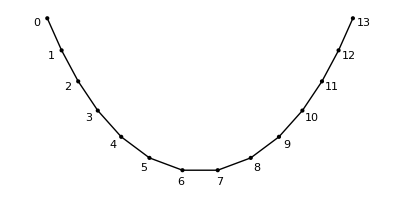

Here, the balls number 0 and N + 1 are held at some fixed points.
	Let us now define a Cartesian coordinate system. First, place the origin at the position of the zeroth ball. Take the z axis to point vertically against the force of gravity, and choose the x axis such that in equilibrium, the chain lies in the x-z plane; finally, take y to be perpendicular to x and z. In other words, just take the coordinate system we’ve used to study a continuous cable. Take the position of the ball N + 1 and call it the point P. Since the ball N + 1 is held in place, the point P is fixed; it’s the same P as in the case of a continuous cable.

### Position of the k-th ball

We know that the distance between two neighboring balls is always the same. Mathematically,

|(r^–)_k - (r^–)_(k-1)| = λ

where (r^–)_k is the position vector of the k-th ball and λ is some constant. Here the zeroth ball is the origin, so (r^–)_0 = 0. We can find λ from the condition that the length of the chain must be equal to L. If we stretch the chain as far as possible, the balls would form a straight line. Since there are N + 1 rods in this chain and each has length λ, the total length will be L = (N + 1)λ.

λ = L/(N + 1)

Now, (r^–)_k - (r^–)_(k-1) is a vector with three components that has to satisfy the constraint of having length λ; in other words, it must lie on the surface of a sphere with radius λ. Thus, we can parametrize it using two angles:

(r^–)_k - (r^–)_(k-1) = λ(Sin[ϕ_k] Cos[θ_k]
Sin[ϕ_k]Sin[θ_k]
-Cos[ϕ_k])

The choice of parametrization is arbitrary, however, for convenience, I chose an analog of spherical coordinates. By taking the norm of the above expression you can verify that its length is identically λ. The figure below illustrates how the angles θ and ϕ can be used to express ((r^–)_k - (r^–)_(k-1))/λ.

-Graphics-

By summing the equation from 0 to k, we arrive at the formula for the position of the k-th ball.

(r^–)_k = (∑^k)_(n = 1)λ (Sin[ϕ_n] Cos[θ_n]
Sin[ϕ_n]Sin[θ_n]
-Cos[ϕ_n])

The two figures below show the angles θ and ϕ can be used to describe the configuration of the chain.

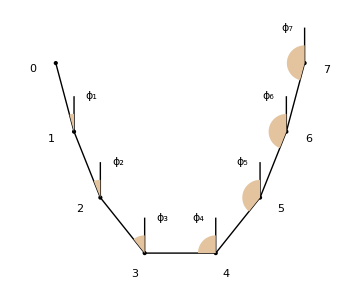
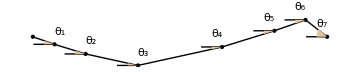
-Graphics-Sight from the +y direction
-Graphics-Sight from above

#### Code used to generate the figures

```mathematica
Table[
	With[{ϕ = 0.9, θ = 0.8}, Rasterize[
		Graphics3D[{
			Arrow[{{0, 0, 0}, {1, 0, 0}}], Text[Style["X", 21], {1.1, 0, 0}],
			Arrow[{{0, 0, 0}, {0, 1, 0}}], Text[Style["Y", 21], {0, 1.1, 0}],
			Arrow[{{0, 0, 0}, {0, 0, 1}}], Text[Style["Z", 21], {0, 0, 1.1}],
			{Thick, Blue, Arrow[{{0, 0, 0}, {Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], -Cos[ϕ]}}]},
			{Opacity[0.3], Sphere[{0, 0, 0}]},
			Polygon[Append[Table[{Cos[θ] Sin[α], Sin[θ] Sin[α], -Cos[α]}, {α, 0, ϕ, ϕ/20}], {0, 0, 0}]],
			Polygon[Append[Table[{Sin[ϕ]Cos[α], Sin[ϕ]Sin[α], -Cos[ϕ]}, {α, 0, θ, θ/20}], {0, 0, -Cos[ϕ]}]],
			{FaceForm[], Polygon[({{Cos[θ], 0, -Sin[θ]}, {Sin[θ], 0, Cos[θ]}, {0, -1, 0}}).Append[#, 0] & /@ CirclePoints[50]]},
			{Dashed, Line[{{Sin[ϕ], 0, 0}, {Sin[ϕ], 0, -Cos[ϕ]}}]},
			Text[Style["θ", 16], {0.8Sin[ϕ] Cos[θ/2], 0.8Sin[ϕ] Sin[θ/2], -Cos[ϕ]}],
			Text[Style["ϕ", 16], 0.2{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], -1-Cos[ϕ]}]
		},
		ViewPoint -> viewpoint, Boxed -> False],
		ImageSize -> {600, 600}
	]],
	{viewpoint, {{1.2, 0.4, 0.4}, {0.2, 2.8, 1.4}}}
] // ImageCollage
```

```mathematica
illustrateϕ[xp_, zp_, L_, Nballs_] := Module[
	{
		λ = L / (Nballs + 1),
		plist = { {0, 0} }, glist,
		currx = 0, currz = 0,
		Svals, Cvals
	},
	{Svals, Cvals} = findSC[xp, zp, L, Nballs];
	
	Table[
		currx += λ Svals[[n]];
		currz -= λ Cvals[[n]];
		
		AppendTo[plist, {currx, currz}],
		{n, Length[Svals]}
	];
	
	glist = Point /@ plist;
	
	glist = Join[glist,
		Table[Line[{#[[n]], #[[n + 1]]}], {n, Length[#] - 1}] &@ plist
	];
	
	glist = Join[glist,
		Table[
			Text[
				ToString[n - 1],
				plist[[n]] - λ/3 Normalize[{(Cvals[[#]] + Cvals[[Max[# - 1, 1]]])/2, (Svals[[#]] + Svals[[Max[# - 1, 1]]])/2}]&@ Min[n, Nballs + 1]
			],
			{n, Nballs + 2}
		]
	];
	
	glist = Join[glist,
		Line[{#, # + {0, λ/2}}]& /@ plist[[2;;]],
		Table[
			{RGBColor[0.89, 0.77, 0.62], Polygon[Append[
				Table[plist[[n]] + λ/4{-Sin[a], Cos[a]}, {a, 0, #, # / 20}]&@ If[Svals[[n - 1]]/Cvals[[n - 1]] ≥ 0, ArcTan[Svals[[n - 1]]/Cvals[[n - 1]]], π - ArcTan[-Svals[[n - 1]]/Cvals[[n - 1]]]],
				plist[[n]]
			]]},
			{n, 2, Length[plist]}
		],
		Table[
			Text[
				Subscript["ϕ", n - 1],
				plist[[n]] + λ/2 If[n > Length[plist]/2, {-1/2, 1}, {1/2, 1}]
			],
			{n, 2, Length[plist]}
		]
	];
	
	Labeled[Graphics[glist, ImageSize -> Medium], "Sight from the +y direction"]
]
```

```mathematica
illustrateθ[xp_, zp_, L_, Nballs_] := Module[
	{
		λ = L / (Nballs + 1),
		plist = { {0, 0} }, glist,
		currx = 0, curry = 0,
		Svals, Cvals,
		θlist
	},
	{Svals, Cvals} = findSC[xp, zp, L, Nballs];
	
	θlist = Array[0.3 CubeRoot[Cos[π/(Nballs + 1) #]]&, Nballs];
	AppendTo[θlist, -(θlist.Svals[[;;-2]])/Svals[[-1]]];
	
	Table[
		currx += λ Svals[[n]];
		curry -= λ Svals[[n]] θlist[[n]];
		
		AppendTo[plist, {currx, curry}],
		{n, Length[Svals]}
	];
	
	glist = Point /@ plist;
	
	glist = Join[glist,
		Table[Line[{#[[n]], #[[n + 1]]}], {n, Length[#] - 1}] &@ plist
	];
	
	glist = Join[glist,
		Line[{#, # - {λ/4, 0}}]& /@ plist[[2;;]],
		Table[
			{RGBColor[0.89, 0.77, 0.62], Polygon[Append[
				Table[plist[[n]] + λ/8{-Cos[a], Sin[a]}, {a, 0, θlist[[n - 1]], θlist[[n - 1]] / 20}],
				plist[[n]]
			]]},
			{n, 2, Length[plist]}
		],
		Table[
			Text[
				Subscript["θ", n - 1],
				plist[[n]] + λ/8 If[n > Length[plist]/2, {-1/2, 1}, {1/2, 1}]
			],
			{n, 2, Length[plist]}
		]
	];
	
	Labeled[Graphics[glist, ImageSize -> Medium], "Sight from above"]
]
```

```mathematica
Column[{illustrateϕ[1, 0, 2, 6], illustrateθ[1, 0, 2, 6]}]
```

### Linear approximation

In this problem, we are only interested in small oscillations near equilibrium. Let us then express the angle ϕ_n in (64) as a sum of its equilibrium value and a small perturbation.

ϕ_n[t] = F_n + φ_n[t]

Here F_n is the value of ϕ_n at equilibrium and φ_n is the small displacement from the equilibrium position. Let us assume that in equilibrium, θ is zero, so that the chain lies in the xz plane (this is proven in the full version, formula 135). Substituting (65) into (64) and taking the first-order approximation, we arrive at the following formula for (r^–)_k.

(r^–)_k = (∑^k)_(n = 1)λ (S_n + C_n φ_n
S_n θ_n
-C_n + S_n φ_n)

where

S_n ≡ Sin[F_n]
C_n ≡ Cos[F_n]

### Boundary conditions

We know that the ball number N + 1 is held at the point P and hence has its xyz coordinates equal to <x_p, 0, z_p>. Using the formula (66), we get

(∑^(N+1))_(n = 1) (S_n
0
-C_n) + (C_n φ_n
S_n θ_n
S_n φ_n) = (x_p/λ
0
z_p/λ)

## Deriving the equations of motion

### Newton’s second law

Newton’s second law for the k-th ball reads

m (d^2(r^–)_k)/dt^2 = (T^–)_(k, k) + (T^–)_(k+1, k) + m g^–

Here (T^–)_(k, k) and (T^–)_(k+1,  k) is the force with which the rods k and k+1 act upon the ball k, respectively. Let us denote T_k the tension in the k-th rod and (l^–)_k the unit vector pointing along the k-th rod. Since the tension forces act along the rods, we can write the above equation as follows. (a proof why tension acts along the rods is given in the full version)

m (d^2(r^–)_k)/dt^2 = T_(k+1)(l^–)_(k+1) - T_k(l^–)_k + m g^–

Using the formula (66), we can write this

mλ (∑^k)_(n = 1) (C_n(φ^(··))_n
S_n(θ^(··))_n
S_n(φ^(··))_n) = T_(k+1)(S_(k+1) + C_(k+1)φ_(k+1)
S_(k+1)θ_(k+1)
-C_(k+1) + S_(k+1)φ_(k+1)) - T_k(S_k + C_k φ_k
S_k θ_k
-C_k + S_k φ_k) + m g (0
0
-1)

### Equations of motion

Combining Newton’s second law (70), the boundary conditions (68), and the requirement that the case φ_k = θ_k = 0 corresponds to the chain being in equilibrium, we obtain the equations of motion. The terms quadratic in ε are neglected.

(θ^(··))_k = -ω_0^2(∑^N)_(n = 1)Y_kn θ_n
(φ^(··))_k = -ω_0^2(∑^(N-1))_(n = 1)K_kn φ_n

Here Y and K are square matrices of dimensions N×N and (N - 1)×(N - 1), respectively, and are defined in (74). ω_0 = √(g/L) is a constant. Notice that ω_0 only depends on the cable’s length and not on where its’ edges are attached. It stays constant for a given cable no matter how the cable is hung, and this is what makes it a natural candidate for a characteristic frequency. The derivation of (71) is given in the chapter “Oscillations of a discrete chain” in the full version of the work. Having computed Y and K, we can compute the natural frequencies and normal modes though the eigenvalues and eigenvectors of the two matrices.

Y_kn ≡ (N(N+1))/(μ S_k)Piecewise[{{δ_n1 - δ_n2, k = 1}, {2 δ_nk - δ_(n, k+1) - δ_(n, k-1), 1 < k < N}, {2 δ_nN + S_n/(S_(N+1)) - δ_(n, N-1), k = N}}]                N > 1
Y_11 = 2/μ(1/S_1 + 1/S_2)                                                                                   N = 1
K_kn = (N(N+1))/μ(∑^(N-1))_(s = 1)(M^-1)_ks G_sn
	M_kn ≡ u_nk(S_n - μ/N(k - n)C_n + (C_(k+1))/(S_(k+1))C_n) -  S_n + μ/N(N - n)C_n - (C_(N+1))/(S_(N+1))C_n + (1 + C_N/S_N(C_(N+1))/(S_(N+1)))(N + 1 - n)S_n
	G_kn ≡ Piecewise[{{(2/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n) + 1/S_n^3 δ_(n, N-1))S_n, k = N-1}, {(1/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n) + 1/S_n^3(δ_nk - δ_(n, k+1)))S_n, k < N-1}}]

Here S and C are defined as

C_k = (-μ k/N + ν)/(√(1+(-μ k/N + ν)^2))                                    S_k = 1/(√(1+(-μ k/N + ν)^2))

where the parameters μ, ν are found from the equations

(∑^(N+1))_(n = 1) 1/(√(1+(-μ n/N + ν)^2)) = x_p/λ                          (∑^(N+1))_(n = 1) (-μ n/N + ν)/(√(1+(-μ n/N + ν)^2)) = -z_p/λ

### Two simple examples

To verify (71), let us take a chain with a small number of elements and manually compute the normal frequencies. If the result we get matches with what we calculated from (71), then the latter is probably correct.

#### Horizontal oscillations

Let us look at a chain with N = 1, z_p = 0:

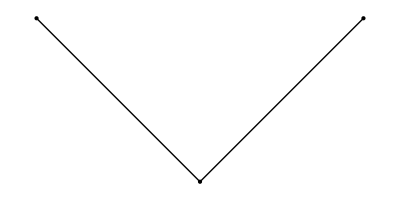

The top two balls are fixed; they are held on the same height, and the horizontal distance between them is x_p. The bottom ball is connected to them via two massless rigid rods of length L/2. The rods are connected with joints. From the picture, it is clear that the system only has one normal mode of oscillations: when the bottom ball is moving into and out of the plane. No in-plane normal modes are present because the system forms a rigid “triangle”.
	From symmetry, the ball can only move in the one vertical plane. Imagining how it would oscillate, it is clear that it would move as a mathematical pendulum with a rod of length √((L/2)^2 - (x_p/2)^2). And as we know, the angular frequency ω of oscillation of such a system is √(g/(√((L/2)^2 - (x_p/2)^2))).
	Let us compute ω for L = 1, g = 1, x_p = 0.5:

```mathematica
With[{L = 1, g = 1, xp = 0.5}, √(g/(√((L/2)^2 - (xp/2)^2)))]
```

1.51967

We want to check the correctness of (71). According to the latter, the angular frequency of the n-th normal mode of in-plane oscillations is given by ω_n = √(g/L λ_n), where λ_n is the n-th eigenvalue of the matrix Y. The function findY[x_p, z_p, L, N] computes the matrix Y using the formula (72), and the code below computes the first normal frequency of in-plane oscillations for L = 1, g = 1, x_p = 0.5 for a chain with N = 1 elements.

```mathematica
With[{L = 1, g = 1, xp = 0.5}, √(g/L First@Eigenvalues[findY[xp, 0, L, 1]])]
```

1.51967

As you can see, the value of ω that we got from (71) is the same as what we calculated manually. Thus, the equation (71) is most likely correct.

#### Vertical oscillations

Let us now look at a chain with L = 1, N = 2:

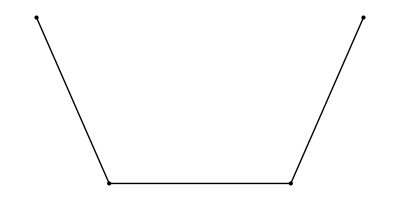

The top two balls are fixed; they are held on the same height, and the horizontal distance between them is x_p. The balls are connected via three massless rigid rods of length l = L/3. The rods are connected with joints. From the picture, it can be seen that the system has one in-plane normal mode. Let us try to find it.
	Denote the angle between the leftmost rod and the vertical as ϕ_1, the angle between the rightmost rod and the vertical - ϕ_2, with ϕ_1 and ϕ_2 taken to be positive in equilibrium. The distance between two bottom balls is l. By the Pythagorean theorem, we have

(x_p - l Sin[ϕ_1] - l Sin[ϕ_2])^2 + (l Cos[ϕ_1] - l Cos[ϕ_2])^2 = l^2

In equilibrium, the chain hangs symmetrically, so ϕ_(1(e)) = ϕ_(2(e)); let’s denote F ≡ ϕ_(1(e)) = ϕ_(2(e)). Demanding the above equality to hold in equilibrium, we obtain x_p/l = 1 + 2 Sin[F]. For small oscillations, the angles ϕ_1 and ϕ_2 only vary by a small amount from their equilibrium value: ϕ_1 = F + φ_1, φ_1 << 1,  and similarly, ϕ_2 = F + φ_2, φ_2 << 1. From the previous equation, we obtain an approximate formula for φ_2 in terms of φ_1:

φ_2 = -φ_1+(1+2 Sin[F]) Tan[F] φ_1^2 + O[φ_1^3]

The Lagrangian of this system is given by L = T - V. The kinetic energy T is the sum of the kinetic energies of the individual balls: T = m/2 v_1^2 + m/2 v_2^2, where v_1 and v_2 are the velocities of the two balls. As it can be seen from the picture, v_1 = l (φ^·)_1 and v_2 = l (φ^·)_2. For the potential energy, we have V = m g z_1 + m g z_2 + C, where z_1 and z_2 are the coordinates z of the two balls and C is an arbitrary constant. As it can be seen from the picture, z_1 = -l Cos[ϕ_1], z_2 = -l Cos[ϕ_2]; let us take C to be 2 m g l Cos[F], so that in equilibrium, V = 0. Substituting the formula for φ_2, which is given above, we arrive at the following formula for the Lagrangian.

L = m l^2 ((φ^·)_1)^2 - m g l 1/2  Sec[F] (2+3 Sin[F]-Sin[3 F])φ_1^2 + O[φ_1^3]

Using the Euler-Lagrange equation, we obtain the equation of motion. Its solution is a sine function with angular frequency

ω = √(3/2 Sec[F] (2+3 Sin[F]-Sin[3 F]) g/L)

where we’ve used the fact that l = L/3. Let us compute ω for L = 1, g = 1, F = π/4:

```mathematica
With[{L = 1, g = 1, F = π/4}, N@√(3/2 Sec[F] (2+3 Sin[F]-Sin[3 F]) g/L)]
```

2.69122

We want to check the correctness of (71). According to the latter, the angular frequency of the n-th normal mode of in-plane oscillations is given by ω_n = √(g/L λ_n), where λ_n is the n-th eigenvalue of the matrix K. The function findK[x_p, z_p, L, N] computes the matrix K using the formula (72), and the code below computes the first normal frequency of in-plane oscillations for L = 1, g = 1, F = π/4 for a chain with N = 2 elements. Here, x_p is set equal to (1 + 2 Sin[F])/3 L to satisfy the condition that the distance between the two oscillating balls is l.

```mathematica
With[{L = 1, g = 1, F = π/4}, √(g/L First@Eigenvalues[findK[(1 + 2 Sin[F])/3 L, 0, L, 2]])]
```

2.69122

As you can see, the value of ω that we got from (71) is the same as what we calculated manually. Thus, the equation (71) is most likely correct.

## From small N to large; comparing to a continuous cable

### Equilibrium configuration

Let us compare the equilibrium shape of a hanging chain to those of a hanging cable of the same length hung between the same two points. We can do that by computing both shapes and drawing them on top of each other. Below are given some examples for various values of N for L = 2, x_p= 1, z_p = 0. You can see that although initially the chain’s shape is rather far from the green line representing the cable, as N increases, the shape of the cable comes closer and closer to the catenary.

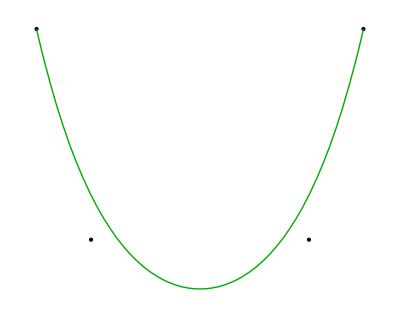
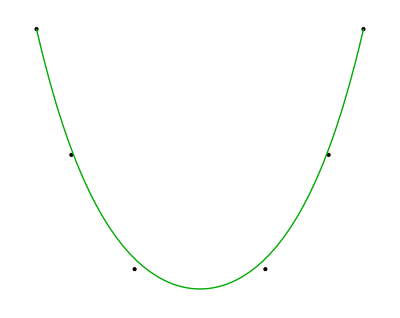
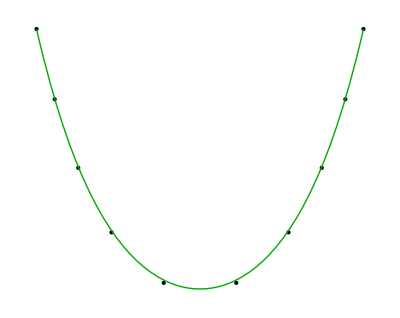
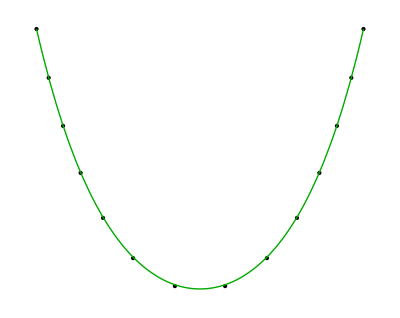

There is an intuitive explanation for that. The potential energy of the chain in the gravitational field is given by U = (∑^N)_(k = 1)m g z_k, where z_k is the z coordinate of the k-th ball. For large N, this sum can be approximated as an integral, and so the potential energy of a hanging chain becomes the same as that of a continuous cable. Next, using the principle of minimum potential energy, we can show that this means that the shape of a chain with a large number of elements is the same as that of a cable.

### Eigenvalues of Y and K and the normal frequencies

The chain’s oscillations are described by the formula (71). Here, the matrix Y and the angles θ_k, 1 ≤ k ≤ N describe the chain’s horizontal oscillations, and the matrix K and the angles φ_k, 1 ≤ k ≤ N - 1 describe the chain’s in-plane oscillations.

(θ^(··))_k = -ω_0^2(∑^N)_(n = 1)Y_kn θ_n
(φ^(··))_k = -ω_0^2(∑^(N-1))_(n = 1)K_kn φ_n

From here, the frequencies of the normal modes of horizontal oscillations are given by ω_n = ω_0 √λ_n, where λ_n is the n-th eigenvalue of the Y matrix, and the same applies to in-plane oscillations. We hypothesize that a chain with a  large number of elements would behave in exactly the same way as a continuous cable, so the frequencies of the normal modes must match, too. While the frequency of the first normal mode of a chain with two free elements will be quite different from that of a continuous cable, the frequency of the first normal mode of a chain with one hundred elements should be very close. As N gets larger, the frequencies of the normal modes approach a certain limit, which is the frequency of oscillations of a continuous cable. And because ω_n = ω_0 √λ_n, this also means that the eigenvalues λ_n of the matrices Y and K must approach some fixed values as N → ∞. Combining it with the fact that the normal modes of a continuous cable are written in terms of dimensionless variables (36) as y[ζ, t] = Λ ψ_n[(ζ - l_0)/Λ] Cos[t/√(Λ/g) ϖ_n] and h[ζ, t] = Λ η_n[(ζ - l_0)/Λ] Cos[t/√(Λ/g) ϖ_n], we arrive at the following conjecture:

λ_n → L/Λ ϖ_n^2                          as N → ∞

We can check this empirically by actually computing the matrices Y and K for various values of N and plotting their eigenvalues as a function of N. We would expect the eigenvalues to asymptote to the values given by the formula above as N → ∞.

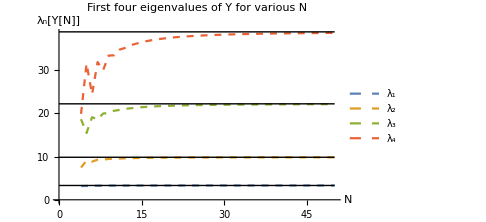
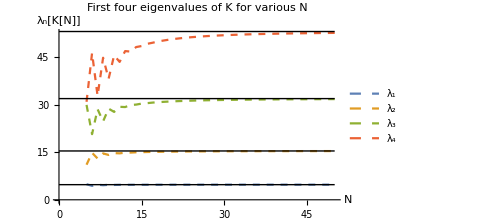

On the two plots above, you can see that the eigenvalues actually do asymptote to the values predicted by (75). The horizontal axis here is N; this is because the matrices Y and K describe the oscillations of a chain with a given number of elements N, and of course the oscillations would be different for chains with different number of elements. In this sense, the matrices Y and K are functions of N. For each value of N, we can also compute the eigenvalues of these matrices, and they two will be functions of N. The plots below show the fist four eigenvalues of Y and K as a function of N. An interesting observation is that the eigenvalues of the K matrix are slightly higher than those of Y, meaning that in-plane oscillations typically have a higher frequency than horizontal oscillations.

#### Code used to generate the last two figures

```mathematica
Block[
	{
		lines = {{}, {}, {}, {}},
		eigvals
	},
	
	Table[
		eigvals = Reverse@Eigenvalues[findY[1, 0, 2, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[4, 50]}
	];
	
	ListLinePlot[lines, PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"}, AxesLabel -> {"N", "λ_n[Y[N]]"}, PlotLabel -> "First four eigenvalues of Y for various N"]
]
```

```mathematica
Block[
	{
		lines = {{}, {}, {}, {}},
		eigvals
	},
	
	Table[
		eigvals = Reverse@Eigenvalues[findK[1, 0, 2, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[5, 50]}
	];
	
	ListLinePlot[lines, PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"}, AxesLabel -> {"N", "λ_n[K[N]]"}, PlotLabel -> "First four eigenvalues of K for various N"]
]
```

```mathematica
Block[
	{
		xp = 1, zp = 0, L = 2,
		lines = {{}, {}, {}, {}},
		eigvals,
		asymptotes,
		Λ, x0, σ0, σp, ϖ
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	σ0 = Sinh[-x0/Λ]; σp = Sinh[(xp - x0)/Λ];
	ϖ = findψNmodes[σ0, σp, 4][[All, 1]];
	asymptotes = L/Λ ϖ^2;
	
	Table[
		eigvals = Reverse@Eigenvalues[findY[xp, zp, L, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[4, 50]}
	];
	
	Show[{
		ListLinePlot[lines,
			PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"},
			AxesLabel -> {"N", "λ_n[Y[N]]"}, 
			PlotLabel -> "First four eigenvalues of Y for various N",
			PlotStyle -> {{Thick, Dashed}}
		],
		Graphics[{Thin, Black, Line[{{0, #}, {50, #}}]}& /@ asymptotes]
	}]
]
```

```mathematica
Block[
	{
		xp = 1, zp = 0, L = 2,
		lines = {{}, {}, {}, {}},
		eigvals,
		asymptotes,
		Λ, x0, σ0, σp, ϖ
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	σ0 = Sinh[-x0/Λ]; σp = Sinh[(xp - x0)/Λ];
	ϖ = findηNmodes[σ0, σp, 4][[All, 1]];
	asymptotes = L/Λ ϖ^2;
	
	Table[
		eigvals = Reverse@Eigenvalues[findK[xp, zp, L, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[5, 50]}
	];
	
	Show[{
		ListLinePlot[lines,
			PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"},
			AxesLabel -> {"N", "λ_n[K[N]]"}, 
			PlotLabel -> "First four eigenvalues of K for various N",
			PlotStyle -> {{Thick, Dashed}}
		],
		Graphics[{Thin, Black, Line[{{0, #}, {50, #}}]}& /@ asymptotes]
	}]
]
```

## Conclusion

## Comparing the numerical results to another article’s

### Normal frequencies of horizontal oscillations

The problem discussed in this work has been explored by John Gregg Gale in his 1976 master's thesis. The methods he used in his work are very different from those used here, however, he also happened to use the same definition of ϖ’s, which he called “natural frequency ratios”. At the end of the article, he provides a series of tables containing the results he obtained for various natural frequencies. We can use this as a reference to confirm the correctness of the present work.
	To make the comparison, let us use the first table for horizontal oscillations:

And here is the same table computed based on the results of this work:

(3.64 | 7.23 | 10.84 | 14.44 | 18.05 | 21.65
2.79 | 5.51 | 8.25 | 11.00 | 13.74 | 16.48
1.91 | 3.74 | 5.59 | 7.44 | 9.29 | 11.15
1.51 | 2.92 | 4.36 | 5.80 | 7.24 | 8.69
1.27 | 2.41 | 3.60 | 4.78 | 5.97 | 7.17
1.09 | 2.05 | 3.06 | 4.07 | 5.08 | 6.09
0.96 | 1.78 | 2.65 | 3.52 | 4.39 | 5.26
0.76 | 1.37 | 2.04 | 2.71 | 3.38 | 4.05
0.62 | 1.06 | 1.60 | 2.11 | 2.63 | 3.16)

This table is generated by calculating the first six normal frequencies ϖ_n for x_p = 0.5, 0.6, 0.7, 0.75, 0.8, 0.85, 0.90, 0.95, 0.97, as in John Gregg Gale’s article. You can see that the two tables are practically identical. Although some entries do vary by around 0.01, the results to match very closely. The values of ϖ predicted by this work are equal to those of John Gregg Gale.

### Normal frequencies of vertical oscillations

And here is the same table computed based on the results of this work:

(6.67 | 9.91 | 13.80 | 17.11 | 20.81 | 24.17
4.52 | 6.92 | 9.61 | 11.99 | 14.56 | 16.95
3.55 | 5.58 | 7.75 | 9.70 | 11.78 | 13.73
2.98 | 4.78 | 6.63 | 8.33 | 10.11 | 11.81
2.59 | 4.23 | 5.87 | 7.40 | 8.97 | 10.49
2.45 | 4.02 | 5.59 | 7.05 | 8.55 | 9.99
2.30 | 3.82 | 5.31 | 6.70 | 8.13 | 9.51
2.09 | 3.50 | 4.87 | 6.16 | 7.48 | 8.75
1.94 | 3.28 | 4.57 | 5.79 | 7.02 | 8.23
1.34 | 2.35 | 3.31 | 4.22 | 5.12 | 6.02
0.98 | 1.76 | 2.50 | 3.21 | 3.91 | 4.60
0.74 | 1.33 | 1.92 | 2.47 | 3.02 | 3.56)

You can see that again, the two tables are practically identical. The difference between this essay’s and John Gregg Gale’s ϖ’s is largest for the sixth normal frequency for the middle rows, when the convergence radius of Frobenius’s method solutions becomes insufficient and numerical solutions have to be used. The numerical error of NDSolve is large for high ϖ’s - that’s why we see high errors there. The place that we should really be worried about is the lowest row, for which σ_0 and σ_p are largest and the cable sags the most. The purpose of (35) was to model the oscillations of a sagging cable, and we see that indeed, for a cable with a large sag it does give the correct result. As we increase ϖ, the error increases, too, but just due to NDSolve’s numerical error - as soon as σ_0 and σ_p get sufficiently small, Frobenius’s method replaces NDSolve, and error immediately vanishes, showing that the equation (35) is also correct for high ϖ’s. Thus, we conclude that the values of ϖ predicted by the current work are, up to a numerical error, equal to those predicted by John Gregg Gale. Since the predictions are extremely unlikely to match by accident, we may conclude that the results presented in this work are correct.

## Novelty and relevance of the work

### Novel things presented in the work

A big advantage of the present essays over past works is that it features interactive visualizations. The reader can experiment with the cable’s or chain’s parameters and see, visually, the system’s equilibrium and modes of oscillation. This makes the content much more intuitive and easy to understand, in addition of course to being entertaining. The demonstrations can be used in classes to illustrate the notion of a normal mode on a system more realistic than a slowly vibrating tight string (in real life, tight strings, such as guitar stings, are in fact so tight that their oscillations are too fast to see) and less complicated than a circular drum. A heavy rope hung on two poles is a very cheap and reliable demonstration and is also thus more practical than many other demonstrations.
	The current work also studies the oscillations of a discrete chain and compares them to those of a continuous cable - something I haven’t seen in other articles. It is interesting to see how a discrete chain approaches a continuous cable as the number of members increases because this touches a very relevant question of how discrete systems with a large number of elements behave. Water, which is made of lots of small molecules, at human scale behaves as if it were continuous. A quantum harmonic oscillator, which has discrete energy levels, does not however have the same thermal energy as its classical analog. A chain with a large number of elements oscillates like a continuous cable. But the emission of thermal radiation happens very differently for atoms with continuous and discrete energy spectra - the “ultraviolet catastrophe”. Sometimes the behavior of discrete systems does approach some limits, sometimes it doesn’t - there probably is not a general principle yet. Maybe, by looking at many examples of how discrete systems do or do not approach some limit we can deduce a general rule?

### Intersections with (and differences from) past works

The problem of an oscillating cable (or a chain, as it’s sometimes called) has been studied in a number of past articles. Perhaps one of the most comprehensive ones available for free is John Gregg  Gale’s master's thesis, written in 1976 in Oregon State University. The author uses methods that are quite different from those used in this work: while the current work describes the cable’s shape through h and y only, Gale’s thesis also makes use of variables representing the cable’s longitudinal displacement and angles. As a result, Gale’s derivation of the equations of motion depends on visual intuition more than the derivation given here, and the equations of motion are written not as two PDEs with one PDE corresponding to one variable but as multiple PDEs of lower order involving not only the cable’s normal displacement but also other variables such as its longitudinal displacement and angles. Each of the resulting equations is shorter than (34) and (35) and hence is somewhat simpler. The equations (35) and (35), however, might be more transparent in that since they only contain y and h, it can be easier to see how the system oscillates - for instance, it’s probably much easier to see how the cable would oscillate if plucked using the equation (35) than using a collection of connected PDEs.
	In Gale’s article, the normal modes of in-plane motion are found in terms the cable’s longitudinal displacement, while in the current work they are found in terms of the cable’s tangential displacement. The approach used in this work has the advantage of being easily visualizable: having found the function h[ζ], we can directly use it to draw the normal mode; having found the tangential displacement as a function of position, however, we have to perform some mathematical manipulations with the result to be able to draw the normal mode.
	Gale coordinatizes the cable through arc length; the work, on the other hand, introduces a curvilinear coordinate system fitted to the cable’s equilibrium. This difference in coordinates is another difference between the current work and Gale’s thesis.
	In his 1953 paper, David Saxon and A. S. Cahn “Modes of vibration of a suspended chain” described an approximate algorithm for finding the normal frequencies of in-plane oscillations. The current article also gives a method for estimating the normal frequencies, namely the formula (59). The formula presented in this work is derived in a comparatively simple way, namely by assuming ψ[σ] and η[σ] to be approximately sinusoidal at a given small interval; the derivation of the formula given by Saxon and Cahn’s article, on the other hand, is quite complicated and involves several pages. It does not, however, contain hypergeometric function as (59) does, so it’s too, in some sense, simpler.
	It is interesting to mention articles on phenomena like conductor galloping, which is when a long electric cable oscillates due to wind, and oscillations of stay bridges. Although the phenomena are in many ways different to the idealized problem discussed in this work, one similarity is that they, too, involve fourth-order partial differential equations. One possible explanation is that maybe, in a cable-type system where both tension and tangential velocity vary, to obtain equations of motion written in terms of tangential displacement only we have to use some conditions, and using them involves differentiation; since we have to take care of two fields, tension and tangential velocity, we differentiate twice and thus end up turning a second-order wave-type equation into a fourth-order PDE. This question would be interesting to explore in future articles.

## Qualitative patterns in the cable’s normal modes

### Greater curvature and amplitude at the lowest point

Here is how the twelfth normal mode of horizontal and in-plane oscillations looks like for σ_0 = -8, σ_p = 8:

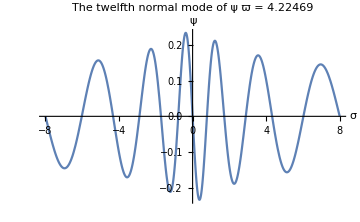
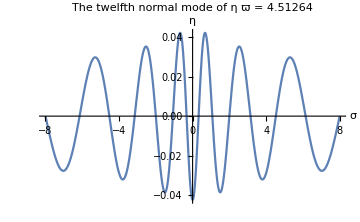

Notice an interesting pattern here: the normal modes oscillate much faster (have greater curvature) near σ = 0 than at the edges, and the amplitude of the oscillations is also larger at the middle. This holds true for different values of σ_0, σ_p and different mode numbers, too. Here is another example, with σ_0 = -4, σ_p = 9:

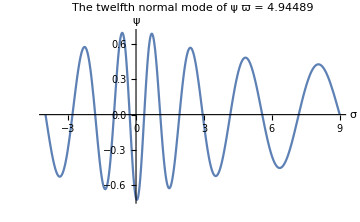
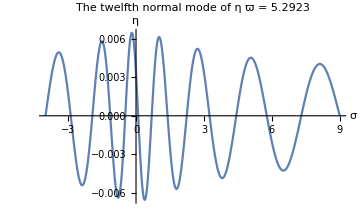

We again see the same thing happening. But why is that? An intuitive explanation goes as follows. Tension in the cable is smallest at the cable’s lowest point, which happens to be the point σ = 0. In a normal mode, the cable oscillates such that at any moment, the acceleration of a piece of cable is proportional to its displacement - we can see it from the formula y[t, ζ] = y[ζ] Cos[ω t], which implies (∂^2 y)/(∂t^2) = -ω^2y. But from Newton’s second law we also know that the acceleration would be a function of the cable’s curvature and tension - more precisely, the acceleration would increase with tension and the difference between the current curvature and equilibrium curvature. Combining the two conclusions, we see that since tension is lowest in the middle, the curvature of the cable must be really high to compensate for that - and this is what we observe in the plots above. The explanation for why the normal modes’ amplitude is greater at the middle is that intuitively, we know that it’s more difficult to get a tight string to oscillate than a string with a small tension. Or, for equal force, a string with a smaller tension would oscillate more than a string with a higher tension. This is a somewhat hand-wavy argument though, and an alternative explanation is given in the section "Approximate algebraic expression for the natural frequencies and normal modes that gets more accurate as the mode number increases or the cable becomes tighter".

### Parity

If the boundary conditions are symmetric, the normal modes of both horizontal and in-plane oscillations will respect parity. Here are some examples:

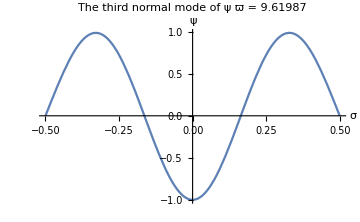
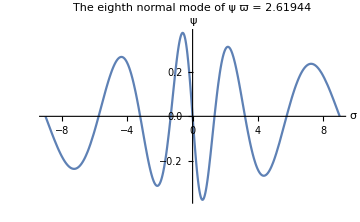
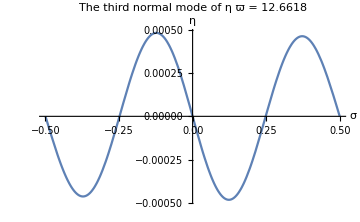
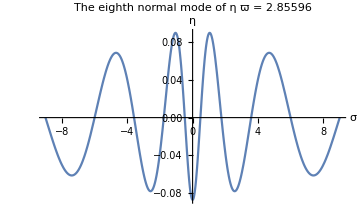
-Graphics- | -Graphics-
-Graphics- | -Graphics-

As long as σ_0 = -σ_p, the normal modes are either even or odd. Intuitively this makes sense: the equations (34) and (35) are symmetric with respect to σ = 0, and as long as boundary conditions do not introduce asymmetry, it makes sense that the normal modes must respect parity. If σ_0 ≠ -σ_p, however, we see that parity is violated:

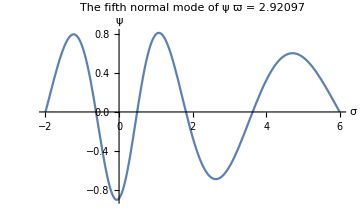

## Qualitative patterns in the chain’s normal modes

In the sections “From small N to large; comparing to a continuous cable” and “Comparing the normal modes as N → ∞, we saw that a chain with a large number of elements oscillates very much like a continuous cable. And indeed, the normal modes tend to have greater “curvature” at the lowest point, and they too have the parity property if the chain is hung symmetrically, as you can see from the two illustrations below.

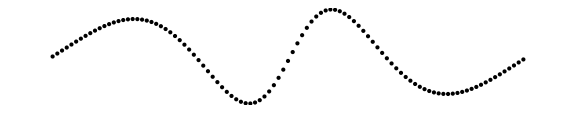
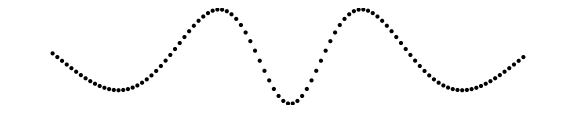
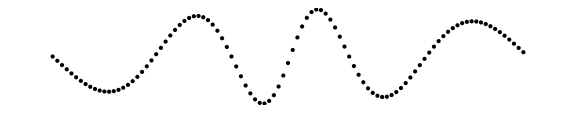

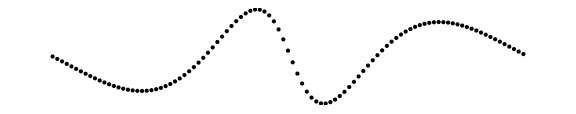
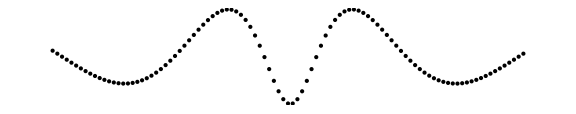
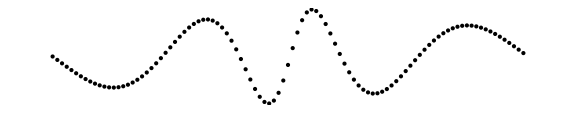

For z_p ≠ 0, you see that parity no longer holds:

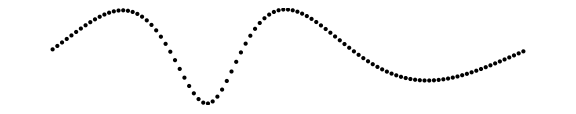
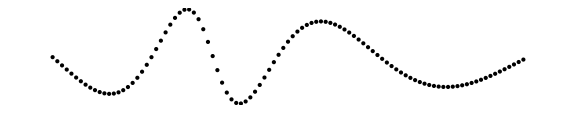
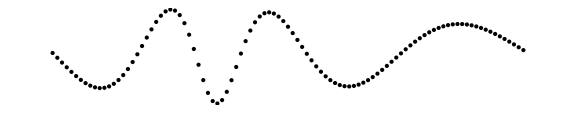

## Open questions

The formula (60) tells us that the normal modes of horizontal oscillations are orthogonal. We also know that the normal modes of a tight string are orthogonal, as well. Is there a general principle or an intuitive explanation for this?
	The equations (42) and (50) take a particularly simple form when written in terms of χ ≡ ArcSinh[σ] and ξ ≡ √(1 + σ^2) - 1: when written in terms of χ, (42) simplifies to (d^2 ψ_n)/dχ^2 + ϖ_n^2 Cosh[χ]ψ_n = 0, and in (50), the coefficient before η becomes zero, effectively reducing it to a third-order equation; when written in terms of ξ, both (42) and (50) have polynomial coefficients. Incidentally, the coordinates χ and ξ also happen to be, up to a linear transformation, Cartesian coordinates. By definition, σ ≡ Sinh[(x - x_0)/Λ], so ξ = (x - x_0)/Λ, which is the horizontal displacement from the cable’s lowest point divided by Λ. By substituting σ = Sinh[(x - x_0)/Λ] into ξ = √(1 + σ^2) - 1, we get ξ = Cosh[(x - x_0)/Λ] - 1. But the formula for z_e[x], which describes the cable’s equilibrium shape, is z_e[x] = Λ Cosh[(x - x_0)/Λ] -Λ Cosh[x_0/Λ]; thus, ξ = (z_e + Λ Cosh[x_0/Λ])/Λ - 1. In other words, ξ is the vertical displacement from the cable’s lowest point. How did it happen that the equation of motion are most simply written in terms of these coordinates? Maybe every system has some “natural coordinates” that can be guessed from physical intuition in which the equations of motion are written in a most simple form?
	Empirically one can observe that the natural frequencies of in-plane motion are, for a given cable, larger than those of horizontal motion. Why is that? Is there a simple explanation?

## References

The University of Utah, “Systems of differential equations”, http://www.math.utah.edu/~gustafso/2250systems-de.pdf
John Gregg Gale, Oregon State University, master’s thesis, 1976, https://ir.library.oregonstate.edu/downloads/6395w964x
UCONN, 2018, https://www.phys.uconn.edu/~rozman/Courses/m3410_18s/downloads/hanging-chain.pdf
Kaldybayev Rauan, 2020, https://community.wolfram.com/groups/-/m/t/2140007?p_p_auth=Jae8g07P
The image of Titanic breaking in half is taken from https://www.britannica.com/story/timeline-of-the-titanics-final-hours

## Bibliography

John Gregg Gale, Oregon State University, master’s thesis, 1976, https://ir.library.oregonstate.edu/downloads/6395w964x
UCONN, “Oscillations of a hanging chain”, 2018, https://www.phys.uconn.edu/~rozman/Courses/m3410_18s/downloads/hanging-chain.pdf
Saxon and Cahn, “Vibrations of a suspended chain”, 1953, The Quarterly Journal of Mechanics and Applied Mathematics, Oxford Academic